# Black hole accretion disks - Isothermal

This notebook will analyse a model of isothermal accretion disks around a black hole.

We first analyse the steady problem, before examining stability in the second part.

## Steady Navier Stokes

### Governing equations

The steady Navier-Stokes equations for a viscous isothermal monoatomic gas accreting around a black hole with Pseudo Newtonian potential are as follows:

```mathematica
U={ur[t,r,θ,z],uθ[t,r,θ,z],uz[t,r,θ,z]};
gradU=Grad[U,{r,θ,z},"Cylindrical"];
strainU=gradU+gradUᵀ;
divU=Div[U,{r,θ,z},"Cylindrical"];
Id=IdentityMatrix[3];
stress=ρ[t,r,θ,z]ν1 divU Id+ρ[t,r,θ,z]ν2 strainU;
viscous=Div[stress,{r,θ,z},"Cylindrical"];
advective=(*Div[ρ[r,θ,z]TensorProduct[U,U],{r,θ,z},"Cylindrical"]*)ρ[t,r,θ,z](D[U, t]+gradU.U);
pressure=Grad[p[t,r,θ,z],{r,θ,z},"Cylindrical"];
gravity={-G M ρ[t,r,θ,z]/(r-rS)^2,0,-G M ρ[t,r,θ,z]/(r-rS)^2 z/r};
navierstokes=advective+pressure-viscous-gravity;
```

We also have the continuity equation

```mathematica
massAdvection=D[ρ[t,r,θ,z], t];
massFlux=Div[ρ[t,r,θ,z] U,{r,θ,z},"Cylindrical"];
continuity=massAdvection+massFlux;
```

We invoke several assumptions to simplify the equations

```mathematica
assumptions={
Derivative[(i_/;i>0),_,_,_][___]:>(0&)(*steady*),
(Derivative[_,_,i_,_][___]:>(0&)/;i>0)(*axisymmetry*),
(*p->(k ρ[#1,#2,#3,#4]^γ&)*)(*adiabatic exponent*)
p->(k ρ[#1,#2,#3,#4]&)(*isothermal*),
ν1->0(*monatomic*),
(Derivative[0,i_,j_,k_][f_]:>(0&)/;(k>0&&FreeQ[f,ρ]&&FreeQ[f,p]))(*no z derivatives for velocity*),
uz:>(0&)(*no vertical velocity*)
};
```

### Hydrostatic balance

First we simplify the equations assuming hydrostatic balance

The vertical momentum equations reads:

```mathematica
Collect[navierstokes[[3]],{ν1,ν2}]
```

(G M z ρ[t,r,θ,z])/(r (r-rS)^2)+p^(0,0,0,1)[t,r,θ,z]+ν1 (-ρ^(0,0,0,1)[t,r,θ,z] (uz^(0,0,0,1)[t,r,θ,z]+(ur[t,r,θ,z]+uθ^(0,0,1,0)[t,r,θ,z])/r+ur^(0,1,0,0)[t,r,θ,z])-ρ[t,r,θ,z] (uz^(0,0,0,2)[t,r,θ,z]+(ur^(0,0,0,1)[t,r,θ,z]+uθ^(0,0,1,1)[t,r,θ,z])/r+ur^(0,1,0,1)[t,r,θ,z]))+ν2 (-2 uz^(0,0,0,1)[t,r,θ,z] ρ^(0,0,0,1)[t,r,θ,z]-2 ρ[t,r,θ,z] uz^(0,0,0,2)[t,r,θ,z]-((uθ^(0,0,0,1)[t,r,θ,z]+(uz^(0,0,1,0)[t,r,θ,z])/r) ρ^(0,0,1,0)[t,r,θ,z])/r-(ρ[t,r,θ,z] (uθ^(0,0,1,1)[t,r,θ,z]+(uz^(0,0,2,0)[t,r,θ,z])/r))/r-(ρ[t,r,θ,z] (ur^(0,0,0,1)[t,r,θ,z]+uz^(0,1,0,0)[t,r,θ,z]))/r+(-ur^(0,0,0,1)[t,r,θ,z]-uz^(0,1,0,0)[t,r,θ,z]) ρ^(0,1,0,0)[t,r,θ,z]-ρ[t,r,θ,z] (ur^(0,1,0,1)[t,r,θ,z]+uz^(0,2,0,0)[t,r,θ,z]))+ρ[t,r,θ,z] (uz[t,r,θ,z] uz^(0,0,0,1)[t,r,θ,z]+(uθ[t,r,θ,z] uz^(0,0,1,0)[t,r,θ,z])/r+ur[t,r,θ,z] uz^(0,1,0,0)[t,r,θ,z]+uz^(1,0,0,0)[t,r,θ,z])

This is simplified using the aforementioned assumptions

```mathematica
verticalBalance=Simplify[navierstokes[[3]]//.assumptions]
```

(G M z ρ[t,r,θ,z])/(r (r-rS)^2)+k ρ^(0,0,0,1)[t,r,θ,z]

This implies an error function vertical dependence, with a characteristic thickness that increases with radius

```mathematica
verticalDensity=ρ->(Subscript[ρ, 0][#2]Exp[(-G M)/(2 k (#2-rS)^2#2)#4^2]&);(*isothermal*)
ρ[t,r,θ,z]/.verticalDensity
```

ⅇ^(-(G M z^2)/(2 k r (r-rS)^2)) ρ_0[r]

```mathematica
verticalBalance/.verticalDensity
```

0

Solving the radial dependence of the centreline density ρ_0(r) requires solving the depth-integrated continuity equation

### Depth-integrated momentum equation

Using hydrostatic balance we can determine a relationship between the depth integrated density ρ(r)=(∫_(-∞))^∞ρ(r,z) dz. Under our assumptions the continuity equation simplifies to

```mathematica
continuity//.assumptions
```

(ur[t,r,θ,z] ρ[t,r,θ,z])/r+ρ[t,r,θ,z] ur^(0,1,0,0)[t,r,θ,z]+ur[t,r,θ,z] ρ^(0,1,0,0)[t,r,θ,z]

We can consider this to be the depth integrated equation (the integrals converge because of the error-function vertical profile). This means the derivative of the mass flux 1/r∂_r (r ρ u_r) is zero, and so is a constant -Ṁ.

```mathematica
densitySolution={ρ->((-Ṁ)/(#2 ur[#1,#2,#3,#4])&)};
```

```mathematica
Simplify[continuity//.assumptions//.densitySolution]
```

0

### Non-dimensionalisation

The final step is to non-dimensionalise the momentum equation.
We assume the scales 
- [u_r]=U_r=[u_θ]=U_θ=√k
- [r]=R=(G M)/(2k)
- ϵ=ν_2/([u_r][r])

```mathematica
dimensionalRescaling={Ur->k^(1/2),
Uθ->Ur;
R->(G M)/(2 Ur^2)}
```

{Ur→√k,R→(G M)/(2 Ur^2)}

```mathematica
nondimensionalRescaling={
ur->(Ur ur[#1,#2/R,#3,#4]&),
uθ->(Ur uθ[#1,#2/R,#3,#4]&),
ρ->(Ρ ρ[#1,#2/R,#3,#4]&),
r->R r,
ν2->Ur R ϵ,
rS->(2 G M)/c^2};
```

```mathematica
tol=uθ->(ℓ[#1,#2,#3,#4]/#2&);
ton=ℓ:>(Integrate[n[#1,#2,#3,#4],#2]&);
```

After rescaling, dividing out the density, and non-dimensionalising, we derive the equations

```mathematica
FullSimplify[Expand[navierstokes[[1]]/(ρ[t,r,θ,z] R^-1 Ur^2)//.assumptions/.densitySolution/.nondimensionalRescaling/.c->(2Ur)/rS^(1/2)/.tol]/.{Derivative[0,i_,0,0][f_][t,r,θ,z]->Derivative[i][f][r],f_[t,r,θ,z]->f[r]}//.dimensionalRescaling]
```

-1/r+2/(r-rS)^2-ℓ[r]^2/r^3+ur[r] ((2 ϵ)/r^2+ur'[r])+(ur'[r] (-1+2 ϵ ur'[r]))/ur[r]-2 ϵ ur''[r]

We do the same for the azimuthal momentum equation

```mathematica
Collect[
Simplify[Expand[navierstokes[[2]]/(ρ[t,r,θ,z] R^-1 Ur^2)//.assumptions/.densitySolution/.nondimensionalRescaling/.c->(2Ur)/rS^(1/2)/.tol]/.{Derivative[0,i_,0,0][f_][t,r,θ,z]->Derivative[i][f][r],f_[t,r,θ,z]->f[r]}],ϵ]
```

(ur[r] ℓ'[r])/r+(ϵ (-(2 ℓ[r] (ur[r]+r ur'[r]))/ur[r]+2 r ℓ'[r]+(r^2 ur'[r] ℓ'[r])/ur[r]-r^2 ℓ''[r]))/r^3

```mathematica
Collect[Expand[r%],ϵ]
```

ur[r] ℓ'[r]+ϵ (-(2 ℓ[r])/r^2-(2 ℓ[r] ur'[r])/(r ur[r])+(2 ℓ'[r])/r+(ur'[r] ℓ'[r])/ur[r]-ℓ''[r])

## Asymptotic Analysis of Steady Problem

### Asymptotic equations

The previous equations can be understood as singular perturbation problems in the small parameter ϵ. We now perform a multiple scale matched asymptotics analysis of the equations.

```mathematica
eqs={Collect[Expand[-1/r+2/(r-γ)^2-ℓ[r]^2/r^3+(-1/ur[r]+ur[r]) ur'[r]+ϵ ((2 ur[r])/r^2+(2 ur'[r]^2)/ur[r]-2 ur''[r])],ϵ],
Collect[
Expand[(*ur[r] (uθ[r]/r+uθ'[r])+ϵ ((ur'[r] (-uθ[r]+r uθ'[r]))/(r ur[r])-uθ''[r])*)
ur[r] ℓ'[r]+ϵ (-(2 ℓ[r])/r^2-(2 ℓ[r] ur'[r])/(r ur[r])+(2 ℓ'[r])/r+(ur'[r] ℓ'[r])/ur[r]-ℓ''[r])],ϵ]}
```

{-1/r+2/(r-γ)^2-ℓ[r]^2/r^3-ur'[r]/ur[r]+ur[r] ur'[r]+ϵ ((2 ur[r])/r^2+(2 ur'[r]^2)/ur[r]-2 ur''[r]),ur[r] ℓ'[r]+ϵ (-(2 ℓ[r])/r^2-(2 ℓ[r] ur'[r])/(r ur[r])+(2 ℓ'[r])/r+(ur'[r] ℓ'[r])/ur[r]-ℓ''[r])}

We proceed by deriving the 
- Reduced problem: (a regular perturbation problem in ϵ at the outer scale r), and
- Layer problem: (a singular perturbation problem, solved by rescaling to a size ϵ internal boundary layer around a shock wave, on the scale x=(r-r_s)/ϵ)

```mathematica
α=1;
```

```mathematica
layerRescale={
ur->(ur[(#1-rs)/ϵ^α]&),
(*uθ->(uθ[(#1-rs)/ϵ]&),*)
ℓ->(ℓ[(#1-rs)/ϵ^α]&),
r->rs+ϵ^α x};
```

Then, for each of the reduced and layer problems, for each velocity u_r, u_θ, we expand u(r)=Σ_k ϵ^k u_k(r), u(x)=Σ_k ϵ^k u_k(x) in formal asymptotic series, and solve each order problem in ϵ order-by-order.

```mathematica
expand={
ur->(Sum[ϵ^(α i)Subscript[ur, i][#],{i,0,2}]&),ℓ->(Sum[ϵ^(α i)Subscript[ℓ, i][#],{i,0,2}]&)
(*uθ->(Sum[ϵ^i Subscript[uθ, i][#],{i,0,2}]&)*)};
```

```mathematica
reducedSeries=(Series[#/.expand,{ϵ,0,1}]&)/@eqs;
```

```mathematica
reducedEqns=Table[(SeriesCoefficient[#,α i]&)/@reducedSeries,{i,0,2}];
```

```mathematica
reducedEqns
```

{{-1/r+2/(r-γ)^2-ℓ_0[r]^2/r^3-ur_0'[r]/ur_0[r]+ur_0[r] ur_0'[r],ur_0[r] ℓ_0'[r]},{(2 ur_0[r])/r^2-(2 ℓ_0[r] ℓ_1[r])/r^3+ur_1[r] ur_0'[r]+(2 ur_0'[r]^2)/ur_0[r]+ur_0[r] ur_1'[r]+(ur_1[r] ur_0'[r]-ur_0[r] ur_1'[r])/ur_0[r]^2-2 ur_0''[r],-(2 ℓ_0[r])/r^2-(2 ℓ_0[r] ur_0'[r])/(r ur_0[r])+(2 ℓ_0'[r])/r+ur_1[r] ℓ_0'[r]+(ur_0'[r] ℓ_0'[r])/ur_0[r]+ur_0[r] ℓ_1'[r]-ℓ_0''[r]},{Indeterminate,Indeterminate}}

```mathematica
layerSeries=(Series[#,{ϵ,0,1}]&)/@(eqs/.layerRescale/.expand);
layerEqns=Table[(SeriesCoefficient[#,α i]&)/@layerSeries,{i,-1,1}];
```

```mathematica
layerSeries
```

{(-ur_0'[x]/ur_0[x]+ur_0[x] ur_0'[x]+(2 ur_0'[x]^2)/ur_0[x]-2 ur_0''[x])/ϵ+(-1/rs+2/(rs-γ)^2-ℓ_0[x]^2/rs^3+ur_1[x] ur_0'[x]+ur_0[x] ur_1'[x]+(ur_1[x] ur_0'[x]-ur_0[x] ur_1'[x])/ur_0[x]^2+(2 (-ur_1[x] ur_0'[x]^2+2 ur_0[x] ur_0'[x] ur_1'[x]))/ur_0[x]^2-2 ur_1''[x])+(x/rs^2-(4 x)/(rs-γ)^3+(2 ur_0[x])/rs^2+(3 x ℓ_0[x]^2-2 rs ℓ_0[x] ℓ_1[x])/rs^4+ur_2[x] ur_0'[x]-((ur_1[x]^2-ur_0[x] ur_2[x]) ur_0'[x])/ur_0[x]^3+ur_1[x] ur_1'[x]+(ur_1[x] ur_1'[x])/ur_0[x]^2-ur_2'[x]/ur_0[x]+ur_0[x] ur_2'[x]+2 (((ur_1[x]^2-ur_0[x] ur_2[x]) ur_0'[x]^2)/ur_0[x]^3-(2 ur_1[x] ur_0'[x] ur_1'[x])/ur_0[x]^2+(ur_1'[x]^2+2 ur_0'[x] ur_2'[x])/ur_0[x])-2 ur_2''[x]) ϵ+O[ϵ]^2,(ur_0[x] ℓ_0'[x]+(ur_0'[x] ℓ_0'[x])/ur_0[x]-ℓ_0''[x])/ϵ+(-(2 ℓ_0[x] ur_0'[x])/(rs ur_0[x])+(2 ℓ_0'[x])/rs+ur_1[x] ℓ_0'[x]+(-(ur_1[x] ur_0'[x])/ur_0[x]^2+ur_1'[x]/ur_0[x]) ℓ_0'[x]+ur_0[x] ℓ_1'[x]+(ur_0'[x] ℓ_1'[x])/ur_0[x]-ℓ_1''[x])+(-(2 ℓ_0[x])/rs^2-2 (((-x/(rs^2 ur_0[x])-ur_1[x]/(rs ur_0[x]^2)) ℓ_0[x]+ℓ_1[x]/(rs ur_0[x])) ur_0'[x]+(ℓ_0[x] ur_1'[x])/(rs ur_0[x]))+ur_2[x] ℓ_0'[x]+(((ur_1[x]^2-ur_0[x] ur_2[x]) ur_0'[x])/ur_0[x]^3-(ur_1[x] ur_1'[x])/ur_0[x]^2+ur_2'[x]/ur_0[x]) ℓ_0'[x]+ur_1[x] ℓ_1'[x]+(-(ur_1[x] ur_0'[x])/ur_0[x]^2+ur_1'[x]/ur_0[x]) ℓ_1'[x]+(2 (-x ℓ_0'[x]+rs ℓ_1'[x]))/rs^2+ur_0[x] ℓ_2'[x]+(ur_0'[x] ℓ_2'[x])/ur_0[x]-ℓ_2''[x]) ϵ+O[ϵ]^2}

```mathematica
DSolve[(u[x]-1/u[x])u'[x]==0,u[x],x]
```

{{u[x]→-1},{u[x]→1},{u[x]→C[1]}}

```mathematica
layerEqns
```

{{-ur_0'[x]/ur_0[x]+ur_0[x] ur_0'[x]+(2 ur_0'[x]^2)/ur_0[x]-2 ur_0''[x],ur_0[x] ℓ_0'[x]+(ur_0'[x] ℓ_0'[x])/ur_0[x]-ℓ_0''[x]},{-1/rs+2/(rs-γ)^2-ℓ_0[x]^2/rs^3+ur_1[x] ur_0'[x]+ur_0[x] ur_1'[x]+(ur_1[x] ur_0'[x]-ur_0[x] ur_1'[x])/ur_0[x]^2+(2 (-ur_1[x] ur_0'[x]^2+2 ur_0[x] ur_0'[x] ur_1'[x]))/ur_0[x]^2-2 ur_1''[x],-(2 ℓ_0[x] ur_0'[x])/(rs ur_0[x])+(2 ℓ_0'[x])/rs+ur_1[x] ℓ_0'[x]+(-(ur_1[x] ur_0'[x])/ur_0[x]^2+ur_1'[x]/ur_0[x]) ℓ_0'[x]+ur_0[x] ℓ_1'[x]+(ur_0'[x] ℓ_1'[x])/ur_0[x]-ℓ_1''[x]},{x/rs^2-(4 x)/(rs-γ)^3+(2 ur_0[x])/rs^2+(3 x ℓ_0[x]^2-2 rs ℓ_0[x] ℓ_1[x])/rs^4+ur_2[x] ur_0'[x]-((ur_1[x]^2-ur_0[x] ur_2[x]) ur_0'[x])/ur_0[x]^3+ur_1[x] ur_1'[x]+(ur_1[x] ur_1'[x])/ur_0[x]^2-ur_2'[x]/ur_0[x]+ur_0[x] ur_2'[x]+2 (((ur_1[x]^2-ur_0[x] ur_2[x]) ur_0'[x]^2)/ur_0[x]^3-(2 ur_1[x] ur_0'[x] ur_1'[x])/ur_0[x]^2+(ur_1'[x]^2+2 ur_0'[x] ur_2'[x])/ur_0[x])-2 ur_2''[x],-(2 ℓ_0[x])/rs^2-2 (((-x/(rs^2 ur_0[x])-ur_1[x]/(rs ur_0[x]^2)) ℓ_0[x]+ℓ_1[x]/(rs ur_0[x])) ur_0'[x]+(ℓ_0[x] ur_1'[x])/(rs ur_0[x]))+ur_2[x] ℓ_0'[x]+(((ur_1[x]^2-ur_0[x] ur_2[x]) ur_0'[x])/ur_0[x]^3-(ur_1[x] ur_1'[x])/ur_0[x]^2+ur_2'[x]/ur_0[x]) ℓ_0'[x]+ur_1[x] ℓ_1'[x]+(-(ur_1[x] ur_0'[x])/ur_0[x]^2+ur_1'[x]/ur_0[x]) ℓ_1'[x]+(2 (-x ℓ_0'[x]+rs ℓ_1'[x]))/rs^2+ur_0[x] ℓ_2'[x]+(ur_0'[x] ℓ_2'[x])/ur_0[x]-ℓ_2''[x]}}

### Zeroth order reduced problem

#### Angular momentum equation

The leading order reduced problem for the angular velocity is a straightforward conservation equation for angular momentum ℓ=r u_θ

```mathematica
reducedEqns[[1,2]]/.Subscript[ℓ, 0]->(ℓ&)
```

0

#### Radial momentum equation

The leading order reduced problem for the radial velocity is also integrable, and corresponds to a conserved quantity e, the specific energy of the fluid.

```mathematica
specificEnergy[r_,u_,l_,g_]:=1/2(u^2+l^2/r^2)-2/(r-g)-Log[r]-Log[-u]
```

```mathematica
Simplify[D[specificEnergy[r,Subscript[ur, 0][r],ℓ,γ],r]-reducedEqns[[1,1]]]/.Subscript[ℓ, 0]->(ℓ&)
```

0

Let’s examine this energy surface

```mathematica
Manipulate[contours=ContourPlot[specificEnergy[Exp[s],-v^(1/2),l0,g0],{s,-3,2},{v,0.01,2}];
sonics=ListPlot[{Log[r],1}/.NSolve[D[specificEnergy[r,u,l0,g0],r]==0,r],PlotStyle->Black];
Show[contours,sonics],
{l0,0.01,1},
{g0,0,1}]
```

Transonic trajectories must pass through saddle-type sonic point (critical points of the specific energy).

However, the layer problem shows that it is possible, under certain conditions, for the solution to rapidly jump between trajectories.

### Zeroth order layer problem

#### Radial momentum

The inner layer problem can also be written as a total derivative

```mathematica
Simplify[layerEqns[[1,1]]-Subscript[ur, 0][x]D[Subscript[ur, 0][x]+1/(Subscript[ur, 0][x]) - 2 (Subscript[ur, 0]'[x])/(Subscript[ur, 0][x]),x]]
```

0

This is a constant coefficient Riccati equation, which is solvable via affine Tanh functions

```mathematica
u0Sol=Subscript[ur, 0]->((u0+1/u0)/2-(u0-1/u0)/2 Tanh[(u0-1/u0)/4(#+x0)]&);
```

```mathematica
Simplify[D[Subscript[ur, 0][x]+1/(Subscript[ur, 0][x]) - 2 (Subscript[ur, 0]'[x])/(Subscript[ur, 0][x]),x]/.u0Sol]
```

0

It is convenient to express the solution in terms of log(-ur_0^+(r_s))=a

```mathematica
cleanup={c->u0+1/u0,d->u0-1/u0,u0->-E^a};
```

```mathematica
FullSimplify[(Subscript[ur, 0][x]/.u0Sol//.cleanup/.x0->0)]
```

-Cosh[a]-Sinh[a] Tanh[1/2 x Sinh[a]]

The key information is that this solution connects (u_(r,0))^+(r_s) to ((u_(r,))_0)^-(r_s)=1/(u_(r,0))^+(r_s). The shock must invert the velocity, implying that any shockwave will be transonic.

```mathematica
Manipulate[Plot[-Cosh[a]-Sinh[a] Tanh[1/2 x Sinh[a]]/.a->1,{x,-10/(a+0.01),10/(a+0.01)},PlotRange->{-4,0}],{a,0,2}]
```

This condition, combined with the requirement that continuous transonic trajectories only exist at the sonic points, allows us to narrow down the possible steady shock locations.

However, in order to understand stability, we must solve the subsequent order problem.

#### Angular momentum

The problem for u_(θ,0) becomes

```mathematica
layerEqns[[1,2]]
```

ur_0[x] ℓ_0'[x]+(ur_0'[x] ℓ_0'[x])/ur_0[x]-ℓ_0''[x]

It’s possible to rewrite this as a total derivative

```mathematica
Simplify[layerEqns[[1,2]]+Subscript[ℓ, 0]'[x]D[Log[D[Subscript[ℓ, 0][x],x]]-(Integrate[Subscript[ur, 0][x],x]+Log[Subscript[ur, 0][x]]),x]]
```

0

We can rearrange further to write

```mathematica
Integrate[Subscript[ur, 0][x],x]+Log[Subscript[ur, 0][x]]-Log[D[Exp[Integrate[Subscript[ur, 0][x],x]],x]]//.{Log[a_ b_]->Log[a]+Log[b],Log[Exp[f_]]->f}
```

0

Hence, the general solution for u_(θ,0) is c_1 e^(∫u_(r,0))+c_2

```mathematica
Subscript[ur, 0][x] Subscript[ℓ, 0]'[x]+(Subscript[ur, 0]'[x] Subscript[ℓ, 0]'[x])/(Subscript[ur, 0][x])-Subscript[ℓ, 0]''[x]/.Subscript[ℓ, 0]->(C[1] Exp[Integrate[Subscript[ur, 0][#],#]]+C[2]&)
```

0

We can write this analytically

```mathematica
Assuming[a>0,Exp[Integrate[-Cosh[a]-Sinh[a] Tanh[1/2 x Sinh[a]],x]]]
```

ⅇ^(-x Cosh[a]) Sech[1/2 x Sinh[a]]^2

```mathematica
Manipulate[Plot[ⅇ^(-x Cosh[a]) Sech[1/2 x Sinh[a]]^2,{x,-10,10}],{a,0,10}]
```

The asymptotic matching conditions require polynomial limiting behaviour as x→±∞, but the function behaves like e^((Cosh[a]-Sinh[a])|x|) as x→-∞. As a is never larger than 2, we know that the only way to satisfy the asymptotic matching boundary conditions is to set c_1. The angular momentum is therefore conserved across a shock!

Demonstrating our solution

```mathematica
Simplify[layerEqns[[1,2]]/.{
Subscript[ur, 0]->(-Cosh[a]-Sinh[a] Tanh[1/2 # Sinh[a]]&),
Subscript[ℓ, 0]->(C[1] ⅇ^(-# Cosh[a]) Sech[1/2 # Sinh[a]]^2+C[2]&)}]
```

0

### First order reduced problem

This is linear, but can only practically be solved numerically

```mathematica
reducedEqns[[2]]
```

{(2 ur_0[r])/r^2-(2 ℓ_0[r] ℓ_1[r])/r^3+ur_1[r] ur_0'[r]+(2 ur_0'[r]^2)/ur_0[r]+ur_0[r] ur_1'[r]+(ur_1[r] ur_0'[r]-ur_0[r] ur_1'[r])/ur_0[r]^2-2 ur_0''[r],-(2 ℓ_0[r])/r^2-(2 ℓ_0[r] ur_0'[r])/(r ur_0[r])+(2 ℓ_0'[r])/r+ur_1[r] ℓ_0'[r]+(ur_0'[r] ℓ_0'[r])/ur_0[r]+ur_0[r] ℓ_1'[r]-ℓ_0''[r]}

```mathematica
reducedEqns
```

{{-1/r+2/(r-γ)^2-ℓ_0[r]^2/r^3-ur_0'[r]/ur_0[r]+ur_0[r] ur_0'[r],ur_0[r] ℓ_0'[r]},{(2 ur_0[r])/r^2-(2 ℓ_0[r] ℓ_1[r])/r^3+ur_1[r] ur_0'[r]+(2 ur_0'[r]^2)/ur_0[r]+ur_0[r] ur_1'[r]+(ur_1[r] ur_0'[r]-ur_0[r] ur_1'[r])/ur_0[r]^2-2 ur_0''[r],-(2 ℓ_0[r])/r^2-(2 ℓ_0[r] ur_0'[r])/(r ur_0[r])+(2 ℓ_0'[r])/r+ur_1[r] ℓ_0'[r]+(ur_0'[r] ℓ_0'[r])/ur_0[r]+ur_0[r] ℓ_1'[r]-ℓ_0''[r]},{Indeterminate,Indeterminate}}

```mathematica
Expand[reducedEqns[[2,1]]/.{Subscript[ur, i_]->Subscript[u, r,i]}/.f_[r]->f]
```

-(2 ℓ_0 ℓ_1)/r^3+(2 u_(r,0))/r^2+u_(r,1) u_(r,0)'+(u_(r,1) u_(r,0)')/(u_(r,0)^2)+(2 (u_(r,0)')^2)/(u_(r,0))-(u_(r,1)')/(u_(r,0))+u_(r,0) u_(r,1)'-2 u_(r,0)''

```mathematica
TeXForm[%]
```

\frac{2 u_{r,0}}{r^2}+\frac{2
   \left(u_{r,0}'\right){}^2}{u_{r,0}}+\
   frac{u_{r,1}
   u_{r,0}'}{u_{r,0}^2}+u_{r,1}
   u_{r,0}'+u_{r,0}
   u_{r,1}'-\frac{u_{r,1}'}{u_{r,0}}-2
   u_{r,0}''-\frac{2 \ell _0 \ell
   _1}{r^3}

```mathematica
Simplify[reducedEqns[[2,2]]/.Subscript[ℓ, 0]->(ℓ&)]
```

-(2 ℓ)/r^2-(2 ℓ ur_0'[r])/(r ur_0[r])+ur_0[r] ℓ_1'[r]

```mathematica
Solve[-(2 ℓ)/r^2-(2 ℓ Subscript[ur, 0]'[r])/(r Subscript[ur, 0][r])+Subscript[ur, 0][r] Subscript[ℓ, 1]'[r]==0,Subscript[ℓ, 1]'[r]]//Expand
```

{{ℓ_1'[r]→(2 ℓ)/(r^2 ur_0[r])+(2 ℓ ur_0'[r])/(r ur_0[r]^2)}}

```mathematica
-(2 ℓ)/r^2-(2 ℓ Subscript[ur, 0]'[r])/(r Subscript[ur, 0][r])+Subscript[ur, 0][r] Subscript[ℓ, 1]'[r]/.Subscript[ur, 0]->(-1/(# ρ[#])&)
```

-(2 ℓ)/r^2+(2 ℓ (ρ[r]+r ρ'[r]))/(r^2 ρ[r])-ℓ_1'[r]/(r ρ[r])

```mathematica
Simplify[-(2 ℓ)/r^2+(2 ℓ (ρ[r]+r ρ'[r]))/(r^2 ρ[r])-(Subscript[ℓ, 1]'[r])/(r ρ[r])/.Subscript[ℓ, 1]->(2ℓ (ρ[#]-Subscript[ρ, ∞])&)]
```

0

```mathematica
Expand[reducedEqns[[2,2]]/.{Subscript[ur, i_]->Subscript[u, r,i]}/.f_[r]->f]
```

-(2 ℓ_0)/r^2+(2 ℓ_0')/r+u_(r,1) ℓ_0'+u_(r,0) ℓ_1'-(2 ℓ_0 u_(r,0)')/(r u_(r,0))+(ℓ_0' u_(r,0)')/(u_(r,0))-ℓ_0''

```mathematica
TeXForm[%]
```

-\frac{2 \ell _0 u_{r,0}'}{r
   u_{r,0}}+\ell _0' u_{r,1}+\ell _1'
   u_{r,0}+\frac{\ell _0'
   u_{r,0}'}{u_{r,0}}-\frac{2 \ell
   _0}{r^2}+\frac{2 \ell _0'}{r}-\ell
   _0''

```mathematica
ℓ[r]+ϵ ρ[r] r^3 D[(ℓ[r]/r^2), r]/.ℓ->(ℓ+ϵ Subscript[ℓ, 1][#]&)/.Subscript[ℓ, 1]->(2 ℓ (ρ[#]-ρ∞)&)/.ρ->(Subscript[ρ, 0][#]+ϵ Subscript[ρ, 1][#]&)/.Subscript[ρ, 1]->(-Subscript[ρ, 0][#](Subscript[u, 1][#])/(Subscript[u, 0][#])&)/.Subscript[ρ, 0]->(-1/(# Subscript[u, 0][#])&)//Simplify//(Series[#,{ϵ,0,2}]&)
```

ℓ-2 (ℓ ρ∞) ϵ-(2 (ℓ (3 u_0[r]+2 r ρ∞ u_0[r]^2+r u_0'[r])) ϵ^2)/(r^2 u_0[r]^3)+O[ϵ]^3

### First order layer problem

#### Rearranging

This problem leads to a key linear operator L which we can show is equivalent to L[ur_1]=ur_1''-1/2(ur_0-1/ur_0+4 ur_0'/ur_0)ur_1'-c/2 ur_0'/ur_0 ur_1=-1/2(1/r_s-2/(r_s-γ)^2+ℓ^2/r_s^3)=g_s

```mathematica
u0SolClean={Subscript[ur, 0]->(-Cosh[a]-Sinh[a] Tanh[1/2 # Sinh[a]]&),
Subscript[ℓ, 0]->(ℓ&)};
```

```mathematica
Loperator=Subscript[ur, 1]''[x]-1/2(Subscript[ur, 0][x]-1/(Subscript[ur, 0][x])+4(Subscript[ur, 0]'[x])/(Subscript[ur, 0][x]))Subscript[ur, 1]'[x]-c/2(Subscript[ur, 0]'[x])/(Subscript[ur, 0][x])Subscript[ur, 1][x];
```

```mathematica
Simplify[layerEqns[[2,1]]/-2-(Loperator+1/2(1/rs-2/(rs-γ)^2+ℓ^2/rs^3))/.u0SolClean//.cleanup]
```

0

```mathematica
Subscript[ur, 0]'[x]/.u0SolClean
```

-1/2 Sech[1/2 x Sinh[a]]^2 Sinh[a]^2

Translation symmetry of the leading order problem automatically implies that ur_0' will be within the kernel of the operator L.

```mathematica
FullSimplify[Loperator/.Subscript[ur, 1]->Derivative[1][Subscript[ur, 0]]//.cleanup/.u0SolClean ]
```

0

#### Wronskian

This operator L can be better understood by determining the Wronskian. We can do this by integrating (the negative of) the coefficient of ur_1’ in the operator L.

```mathematica
p[x_,a_]=FullSimplify[1/2 TrigToExp[Subscript[ur, 0][x]-1/(Subscript[ur, 0][x])+4(Subscript[ur, 0]'[x])/(Subscript[ur, 0][x])]/.u0SolClean]
```

-1/2 Sech[1/2 x Sinh[a]] Sech[a+1/2 x Sinh[a]] Sinh[a] (-2 Sinh[a]+Sinh[a+x Sinh[a]])

```mathematica
Assuming[a>0,Integrate[p[x,a],x]]
```

-3 Log[Cosh[1/2 x Sinh[a]]]+Log[Cosh[a+1/2 x Sinh[a]]]

```mathematica
FullSimplify[1/(Subscript[ur, 0][x]Subscript[ur, 0]'[x])Exp[-3 Log[Cosh[1/2 x Sinh[a]]]+Log[Cosh[a+1/2 x Sinh[a]]]]/.u0SolClean,a>0]
```

2 Csch[a]^2

```mathematica
(Cosh[a+1/2 x Sinh[a]] Sech[1/2 x Sinh[a]]^3)/(Subscript[ur, 0][x] Subscript[ur, 0]'[x])
```

(Cosh[a+1/2 x Sinh[a]] Sech[1/2 x Sinh[a]]^3)/(ur_0[x] ur_0'[x])

Thus the Wronskian for L is W=2 (cosech(a))^2 ur_0 ur_0'.

#### Second kernel component

Knowledge of the Wronksian allows us to determine the remaining component of the kernel, by noting that the Wronskian is also given by W=v_1' v_2-v_1 v_2', where v_1,v_2 are the two elements of the kernel of L.

Dividing out ur_0' allows us to simplify the equation to ur_0=u_12 ur_0''/ur_0'-u_12'
 We find that the remaining kernel component is proportional to ur_0+x ur_0'-2/c.

```mathematica
FullSimplify[Subscript[ur, 0][x]-(Subscript[ur, 0]''[x])/(Subscript[ur, 0]'[x]) Subscript[ur, 1][x]+Subscript[ur, 1]'[x]==0/.u0SolClean]
```

Cosh[a]+Sinh[a] Tanh[1/2 x Sinh[a]]==Sinh[a] Tanh[1/2 x Sinh[a]] ur_1[x]+ur_1'[x]

```mathematica
Subscript[ur, 0][x]+Subscript[ur, 1]'[x]==(Subscript[ur, 1][x] Subscript[ur, 0]''[x])/(Subscript[ur, 0]'[x])
```

ur_0[x]+ur_1'[x]==(ur_1[x] ur_0''[x])/ur_0'[x]

```mathematica
u1Sol=DSolve[FullSimplify[Subscript[ur, 0][x]-(Subscript[ur, 0]''[x])/(Subscript[ur, 0]'[x]) Subscript[ur, 1][x]+Subscript[ur, 1]'[x]==0/.u0SolClean],Subscript[ur, 1],x][[1]];
```

```mathematica
FullSimplify[(C[1] Sech[1/2 x Sinh[a]]^2+1/2 Sech[1/2 x Sinh[a]]^2 (x Cosh[a]+Csch[a] Sinh[a+x Sinh[a]]))/(Subscript[ur, 0][x]+x Subscript[ur, 0]'[x]-2/c)//.cleanup/.C[1]->1/2/.u0SolClean]
```

-Coth[a] Csch[a]

```mathematica
(Coth[a] Sech[1/2 x Sinh[a]]^2 (Sinh[a]+x Cosh[a] Sinh[a]+Sinh[a+x Sinh[a]]))/(2+2 Cosh[a] (Subscript[ur, 0][x]+x Subscript[ur, 0]'[x]))
```

(Coth[a] Sech[1/2 x Sinh[a]]^2 (Sinh[a]+x Cosh[a] Sinh[a]+Sinh[a+x Sinh[a]]))/(2+2 Cosh[a] (ur_0[x]+x ur_0'[x]))

We verify that this is the remaining element of the kernel

```mathematica
u1SolClean=Subscript[ur, 1]->(Subscript[ur, 0][#]+# Subscript[ur, 0]'[#]+Sech[a]&);
```

```mathematica
FullSimplify[Loperator//.cleanup/.u1SolClean/.u0SolClean]
```

0

```mathematica
FullSimplify[(Subscript[ur, 0]'[x]Subscript[ur, 1]'[x]-Subscript[ur, 0]''[x]Subscript[ur, 1][x])/(Subscript[ur, 0][x]Subscript[ur, 0]'[x])/.u1SolClean/.u0SolClean]
```

Sinh[a] Tanh[a]

#### Inhomogeneous term

With knowledge of the kernel of L, we can now determine the inhomogeneous solution to L[ur_1]=1 through variation of parameters. 

Specifically, we write ur_1=c_1 ur_11+c_2 u_12, with the condition c_1' ur_11+c_2' u_12=0, and solve these equations simultaneously for c_1 to determine ur_1 (here ur_11=ur_0', u_12=ur_0+x ur_0'-2/c). These equations can be written as expressing c_i' in terms of the Wronskian.

[ur_11' | u_12'
ur_11 | u_12][c_1'
c_2']=[0
1] ⇒[c_1'
c_2']=1/W[-u_12
ur_11] 

We then integrate the equations for c_i, and multiply by the constant g_s to complete the solution.

c_1'=-u_12/W=-ur_0/W-(x ur_0')/W+2/(c W)∝-1/ur_0-x/ur_0+2/c 1/(ur_0 ur_0')

∫-1/ur_0' dx

```mathematica
Expand[Integrate[-1/(Subscript[ur, 0]'[x])/.u0SolClean,x]]
```

x Csch[a]^2+Csch[a]^3 Sinh[x Sinh[a]]

∫-x/ur_0 dx

```mathematica
FullSimplify[Integrate[x/(-Subscript[ur, 0][x])/.u0SolClean/.a->Log[-u0],x],{u0<-1,x∈Reals}]
```

-(x (x+4 u0 (Log[1-(ⅈ ⅇ^(((-1+u0^2) x)/(4 u0)))/u0]+Log[1+(ⅈ ⅇ^(((-1+u0^2) x)/(4 u0)))/u0])))/(2 u0)-(4 u0 PolyLog[2,-(ⅇ^(((-1+u0^2) x)/(2 u0)))/u0^2])/(-1+u0^2)

```mathematica
FullSimplify[Log[Exp[
Log[1-(ⅈ ⅇ^(((-1+u0^2) x)/(4 u0)))/u0]+Log[1+(ⅈ ⅇ^(((-1+u0^2) x)/(4 u0)))/u0]]],{u0<-1,x∈Reals}]
```

Log[1+(ⅇ^(((-1+u0^2) x)/(2 u0)))/u0^2]

```mathematica
Expand[FullSimplify[-(x (x+4 u0 (Log[1+(ⅇ^(((-1+u0^2) x)/(2 u0)))/u0^2])))/(2 u0)-(4 u0 PolyLog[2,-(ⅇ^(((-1+u0^2) x)/(2 u0)))/u0^2])/(-1+u0^2)/.u0->-E^a,{a>0}]]
```

1/2 ⅇ^-a x^2-2 x Log[1+Cosh[2 a+x Sinh[a]]-Sinh[2 a+x Sinh[a]]]+2 Csch[a] PolyLog[2,-Cosh[2 a+x Sinh[a]]+Sinh[2 a+x Sinh[a]]]

```mathematica
Simplify[TrigToExp[Cosh[2 a+x Sinh[a]]-Sinh[2 a+x Sinh[a]]]]
```

ⅇ^(-2 a-1/2 (-ⅇ^-a+ⅇ^a) x)

```mathematica
Simplify[D[1/2 ⅇ^-a x^2-2 x Log[1+ⅇ^(-2 a-Sinh[a] x)]+2 Csch[a] PolyLog[2,-ⅇ^(-2 a-Sinh[a] x)],x]+x/(Subscript[ur, 0][x])/.u0SolClean]
```

0

∫2/c 1/(ur_0 ur_0')

```mathematica
Collect[-FullSimplify[Sech[a]Integrate[1/(Subscript[ur, 0][x]Subscript[ur, 0]'[x])/.u0SolClean,x]],x]
```

-4 Log[Cosh[a+1/2 x Sinh[a]]] Sech[a]+x (-2 Csch[a]^2+1/4 Csch[a]^3 Sech[a] Sinh[4 a])+Csch[a]^3 Sech[a] Sinh[a-x Sinh[a]]

All together

```mathematica
Expand[FullSimplify[(x Csch[a]^2+Csch[a]^3 Sinh[x Sinh[a]])+(1/2 ⅇ^-a x^2-2 x Log[1+ⅇ^(-2 a-Sinh[a] x)]+2 Csch[a] PolyLog[2,-ⅇ^(-2 a-Sinh[a] x)])+(-4 Log[Cosh[a+1/2 x Sinh[a]]] Sech[a]+x (-2 Csch[a]^2+1/4 Csch[a]^3 Sech[a] Sinh[4 a])+Csch[a]^3 Sech[a] Sinh[a-x Sinh[a]]),{a>0,x∈Reals}]]
```

2 x+1/2 ⅇ^-a x^2-2 x Log[1+ⅇ^(-2 a-x Sinh[a])]+2 Csch[a] PolyLog[2,-ⅇ^(-2 a-x Sinh[a])]+Cosh[x Sinh[a]] Csch[a]^2 Sech[a]-4 Log[Cosh[a+1/2 x Sinh[a]]] Sech[a]

c_2'=ur_11/W=ur_0'/W∝1/ur_0

```mathematica
Integrate[1/(Subscript[ur, 0][x])/.u0SolClean,x]
```

-x Cosh[a]+2 Log[Cosh[a+1/2 x Sinh[a]]]

```mathematica
c1[x_,a_]=2 x+1/2 ⅇ^-a x^2-2 x Log[1+ⅇ^(-2 a-x Sinh[a])]+2 Csch[a] PolyLog[2,-ⅇ^(-2 a-x Sinh[a])]+Cosh[x Sinh[a]] Csch[a]^2 Sech[a]-4 Log[Cosh[a+1/2 x Sinh[a]]] Sech[a];
c2[x_,a_]=-x Cosh[a]+2 Log[Cosh[a+1/2 x Sinh[a]]];
```

```mathematica
c1[x,a]
```

2 x+1/2 ⅇ^-a x^2-2 x Log[1+ⅇ^(-2 a-x Sinh[a])]+2 Csch[a] PolyLog[2,-ⅇ^(-2 a-x Sinh[a])]+Cosh[x Sinh[a]] Csch[a]^2 Sech[a]-4 Log[Cosh[a+1/2 x Sinh[a]]] Sech[a]

```mathematica
c1o=c1[x]//ExpToTrig//FullSimplify
```

c1[x]

```mathematica
c1[x,a]Subscript[ur, 0]'[x]+c2[x,a]Subscript[ur, 1][x]/.u1SolClean/.u0SolClean
```

-1/2 (2 x+1/2 ⅇ^-a x^2-2 x Log[1+ⅇ^(-2 a-x Sinh[a])]+2 Csch[a] PolyLog[2,-ⅇ^(-2 a-x Sinh[a])]+Cosh[x Sinh[a]] Csch[a]^2 Sech[a]-4 Log[Cosh[a+1/2 x Sinh[a]]] Sech[a]) Sech[1/2 x Sinh[a]]^2 Sinh[a]^2+(-x Cosh[a]+2 Log[Cosh[a+1/2 x Sinh[a]]]) (-Cosh[a]+Sech[a]-1/2 x Sech[1/2 x Sinh[a]]^2 Sinh[a]^2-Sinh[a] Tanh[1/2 x Sinh[a]])

```mathematica
Manipulate[Plot[-1/2 (2 x+1/2 ⅇ^-a x^2-2 x Log[1+ⅇ^(-2 a-x Sinh[a])]+2 Csch[a] PolyLog[2,-ⅇ^(-2 a-x Sinh[a])]+Cosh[x Sinh[a]] Csch[a]^2 Sech[a]-4 Log[Cosh[a+1/2 x Sinh[a]]] Sech[a]) Sech[1/2 x Sinh[a]]^2 Sinh[a]^2+(-x Cosh[a]+2 Log[Cosh[a+1/2 x Sinh[a]]]) (-Cosh[a]+Sech[a]-1/2 x Sech[1/2 x Sinh[a]]^2 Sinh[a]^2-Sinh[a] Tanh[1/2 x Sinh[a]]),{x,-10/(a+0.01),10/(a+0.01)}],{a,0.001,2}]
```

```mathematica
u1i[x_]=(c1[x,a]Subscript[ur, 0]'[x]+c2[x,a]Subscript[ur, 1][x]/.u1SolClean/.u0SolClean)
```

-1/2 (2 x+1/2 ⅇ^-a x^2-2 x Log[1+ⅇ^(-2 a-x Sinh[a])]+2 Csch[a] PolyLog[2,-ⅇ^(-2 a-x Sinh[a])]+Cosh[x Sinh[a]] Csch[a]^2 Sech[a]-4 Log[Cosh[a+1/2 x Sinh[a]]] Sech[a]) Sech[1/2 x Sinh[a]]^2 Sinh[a]^2+(-x Cosh[a]+2 Log[Cosh[a+1/2 x Sinh[a]]]) (-Cosh[a]+Sech[a]-1/2 x Sech[1/2 x Sinh[a]]^2 Sinh[a]^2-Sinh[a] Tanh[1/2 x Sinh[a]])

```mathematica
Manipulate[
Plot[Evaluate[{uif[x],
u1i[x]}/.a->b],{x,-10,10}],
{b,0,3}]
```

Infinity::indet: Indeterminate expression 2 x+x^2/2+ComplexInfinity+ComplexInfinity-2 x Log[2] encountered.

```mathematica
Simplify[Expand[D[u1i[x],{x,2}]-1/2 (-1/(Subscript[ur, 0][x])+Subscript[ur, 0][x]+(4 Subscript[ur, 0]'[x])/(Subscript[ur, 0][x]))D[u1i[x],x]-c/2 (Subscript[ur, 0]'[x])/(Subscript[ur, 0][x])u1i[x]/.u0SolClean//.cleanup]]
```

Sinh[a] Tanh[a]

We have therefore determined the inhomogeneous solution, which must be divided by sinh a tanh a, and multiplied by g_s.

#### Self adjoint form

The limiting asymptotic boundary conditions constrain the zeroth order shift x_0 as well as the amplitude of the second kernel component u_12. As ur_11 decays exponentially fast toward the boundaries, it cannot be determined by boundary conditions at any order. Instead it is determined through a solvability condition at subsequent order. Such solvability conditions are most easily determined for self-adjoint operators. We now put L into self-adjoint form by dividing through by the Wronskian.

If L=v''-p v'-q v, the Wronskian satisfies W'=p W. Therefore, dividing by W gives 1/W v''-p/W v'-q/W v=(v'/W)'-q/W v.

Integrating by parts shows that this operator is now self adjoint.

```mathematica
LSAoperator=D[((Subscript[ur, 1]'[x])/(Subscript[ur, 0][x]Subscript[ur, 0]'[x])),x]-c/(2(Subscript[ur, 0][x])^2)Subscript[ur, 1][x];
```

We can verify that this operator possesses the same kernel

```mathematica
Simplify[LSAoperator/.Subscript[ur, 1]->Subscript[ur, 0]'/.u0SolClean//.cleanup]
```

0

```mathematica
Simplify[LSAoperator/.u1SolClean/.u0SolClean//.cleanup]
```

0

#### Angular equation

```mathematica
Collect[layerEqns[[2,2]]/.f_[x]->f,{Subscript[ℓ, 1]'',Subscript[ℓ, 1]'}]
```

-(2 ℓ_0 ur_0')/(rs ur_0)+(2 ℓ_0')/rs+ur_1 ℓ_0'+(-(ur_1 ur_0')/ur_0^2+ur_1'/ur_0) ℓ_0'+(ur_0+ur_0'/ur_0) ℓ_1'-ℓ_1''

```mathematica
%/.{Subscript[ℓ, 0]'->0,Subscript[ℓ, 0]->ℓ}
```

-(2 ℓ ur_0')/(rs ur_0)+(ur_0+ur_0'/ur_0) ℓ_1'-ℓ_1''

We’ve already found the kernel of this operator: constants, and e^(∫u_(r,0)dx). It’s possible to invert this operator and integrate by parts to find the general solution

```mathematica
v[x_]:=(2ℓ)/rs(Exp[Integrate[Subscript[ur, 0][x],x]]Integrate[Exp[-Integrate[Subscript[ur, 0][x],x]],x])
```

```mathematica
Simplify[layerEqns[[2,2]]/.u0SolClean[[2]]/.Subscript[ℓ, 1]->v]
```

0

This expression can be simplified to

```mathematica
Simplify[v[x]/.u0SolClean]
```

1/(2 rs)ℓ (2+Cosh[x Sinh[a]]+Cosh[2 a-x Sinh[a]]) Sech[a] Sech[1/2 x Sinh[a]]^2

```mathematica
Simplify[Cosh[x Sinh[a]]+Cosh[2 a-x Sinh[a]]]
```

2 Cosh[a] Cosh[a-x Sinh[a]]

```mathematica
v[x_]:=1/rs ℓ (Sech[a]+Cosh[a-x Sinh[a]])  Sech[1/2 x Sinh[a]]^2
```

```mathematica
FullSimplify[layerEqns[[2,2]]/.u0SolClean/.Subscript[ℓ, 1]->v]
```

0

```mathematica
Manipulate[Plot[(Sech[a]+Cosh[a-x Sinh[a]])  Sech[1/2 x Sinh[a]]^2,{x,-10/(a+.001),10/(a+.001)}],{a,0,2}]
```

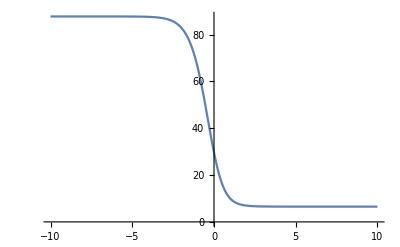

```mathematica
Plot[v[x]/.{ℓ->1.1,rs->0.092,a->1.3},{x,-10,10}]
```

This expression could likely be written entirely in terms of u_(r,0), u_(r,0)' and other constants, but I’m not sure I can be bothered figuring it out.

```mathematica
Manipulate[Plot[(Sech[a]+Cosh[a-x Sinh[a]])  Sech[1/2 x Sinh[a]]^2,{x,-10/(Sinh[a]+.01),10/(Sinh[a]+.01)},AxesOrigin->{0,0}],{a,0,2}]
```

This gives us a boundary condition to solve ℓ^- for r<r_s.

#### m variable

```mathematica
(ρ[r](1+u[r]^2-2ϵ D[(r u[r]), r]/r)/.{ρ->(ρ[(#-rs)/ϵ]&),u->(u[(#-rs)/ϵ]&)}/.r->rs+ϵ x/.{ρ->(Sum[ϵ^i Subscript[ρ, i][#],{i,0,1}]&),u->(Sum[ϵ^i Subscript[u, i][#],{i,0,1}]&)}//(Series[#,{ϵ,0,1}]&)
)/.Subscript[ρ, 0]->(-1/(rs Subscript[u, 0][#])&)//Simplify//Expand
```

-(1+u_0[x]^2-2 u_0'[x])/(rs u_0[x])+(-(2 u_1[x])/rs+ρ_1[x] (1+u_0[x]^2-2 u_0'[x])+(2 (1+(rs u_1'[x])/u_0[x]))/rs^2) ϵ+O[ϵ]^2

Simplify zeroth order term m_0

```mathematica
Expand[-(1+(Subscript[u, 0][x])^2-2 Subscript[u, 0]'[x])/(rs Subscript[u, 0][x])]/.Subscript[u, 0]->(-Cosh[a]-Sinh[a]Tanh[1/2 Sinh[a] #]&)//FullSimplify
```

(2 Cosh[a])/rs

Simplify first order term m_1

```mathematica
-(2 Subscript[u, 1][x])/rs+Subscript[ρ, 1][x] (1+(Subscript[u, 0][x])^2-2 Subscript[u, 0]'[x])+(2 (1+(rs Subscript[u, 1]'[x])/(Subscript[u, 0][x])))/rs^2/.Subscript[u, 0]->(-Cosh[a]-Sinh[a]Tanh[1/2 Sinh[a] #]&)//FullSimplify
```

-(2 u_1[x])/rs+2 Cosh[a] (Cosh[a]+Sinh[a] Tanh[1/2 x Sinh[a]]) ρ_1[x]+(2-(2 rs u_1'[x])/(Cosh[a]+Sinh[a] Tanh[1/2 x Sinh[a]]))/rs^2

#### n variable

```mathematica
((ℓ[r]+ϵ ρ[r] r^3 D[(ℓ[r]/r^2), r])/.{ρ->(ρ[(#-rs)/ϵ]&),
ℓ->(ℓ[(#-rs)/ϵ]&),u->(u[(#-rs)/ϵ]&)}/.r->rs+ϵ x/.{ρ->(Sum[ϵ^i Subscript[ρ, i][#],{i,0,1}]&),ℓ->(Sum[ϵ^i Subscript[ℓ, i][#],{i,0,1}]&),u->(Sum[ϵ^i Subscript[u, i][#],{i,0,1}]&)}//(Series[#,{ϵ,0,1}]&)
)//.{Subscript[ρ, 0]->(-1/(rs Subscript[u, 0][#])&),Subscript[ℓ, 0]->(ℓ&)}//Simplify//Expand
```

ℓ+(ℓ_1[x]+((2 ℓ)/rs-ℓ_1'[x])/u_0[x]) ϵ+O[ϵ]^2

ℓ+(ℓ_1[x]+((2 ℓ)/rs-ℓ_1'[x])/u_0[x]) ϵ+O[ϵ]^2

Simplify first order term n_1

```mathematica
Expand[Subscript[ℓ, 1][x]+((2 ℓ)/rs-Subscript[ℓ, 1]'[x])/(Subscript[u, 0][x])]/.{Subscript[u, 0]->(-Cosh[a]-Sinh[a]Tanh[1/2 Sinh[a] #]&),
Subscript[ℓ, 1]->(ℓ/rs(Sech[a]+Cosh[a-Sinh[a]#])Sech[Sinh[a]#/2]^2&)}//FullSimplify
```

0

## Stability analysis

### Evolution equation derivation

We now rederive evolution equations without assuming steady solutions. It will be convenient to keep in first order form in time by defining three variables of interest, the velocity u, the logarithmic density δ=log ρ, and the strain(?) q.

```mathematica
logDensity=ρ->(Subscript[ρ, 0] Exp[δ[#1,#2,#3,#4]]&);
```

```mathematica
Collect[Expand[navierstokes[[1]]/ρ[t,r,θ,z]//.assumptions[[2;;]]/.logDensity],ν2]
```

(G M)/(r-rS)^2-uθ[t,r,θ,z]^2/r+ur[t,r,θ,z] ur^(0,1,0,0)[t,r,θ,z]+k δ^(0,1,0,0)[t,r,θ,z]+ν2 ((2 ur[t,r,θ,z])/r^2-(2 ur^(0,1,0,0)[t,r,θ,z])/r-2 ur^(0,1,0,0)[t,r,θ,z] δ^(0,1,0,0)[t,r,θ,z]-2 ur^(0,2,0,0)[t,r,θ,z])+ur^(1,0,0,0)[t,r,θ,z]

The continuity equation becomes

```mathematica
Simplify[continuity/ρ[t,r,θ,z]//.assumptions[[2;;]]/.logDensity]
```

ur^(0,1,0,0)[t,r,θ,z]+ur[t,r,θ,z] (1/r+δ^(0,1,0,0)[t,r,θ,z])+δ^(1,0,0,0)[t,r,θ,z]

### Nondimensionalisation

We assume the scales 
- [u_r]=U_r=[u_θ]=U_θ=k^(1/2)
- [r]=R=(G M)/(2k)
- [t]=[r]/[u_r]=(G M)/(2 k^(3/2))
- ϵ=ν_2/([u_r][r])

```mathematica
Ur=k^(1/2);
Uθ=k^(1/2);
R=(G M)/(2 k);
T=R/Ur;
```

```mathematica
nondimensionalRescaling={

ur->(Ur ur[#1/T,#2/R,#3,#4]&),
uθ->(Uθ uθ[#1/T,#2/R,#3,#4]&),
δ->(δ[#1/T,#2/R,#3,#4]&),
r->R r,
t->T t,
ν2->Ur R ϵ,
rS->(2 G M)/c^2};
```

```mathematica
tol=uθ->(ℓ[#1,#2,#3,#4]/#2&);
ton=ℓ:>(Integrate[n[#1,#2,#3,#4],#2]&);
keepl={Integrate[ Derivative[i_,0,0,0][n][t,r,θ,z],r]:> Derivative[i,0,0,0][ℓ][t,r,θ,z],
Integrate[n[t,r,θ,z],r]:> ℓ[t,r,θ,z]};
toq=ur->(1/#2 Integrate[#2 q[#1,#2,#3,#4],#2]&);
keepu= {Integrate[r Derivative[i_,0,0,0][q][t,r,θ,z],r]:>r Derivative[i,0,0,0][ur][t,r,θ,z],
Integrate[r q[t,r,θ,z],r]:>r ur[t,r,θ,z]};
unsteadyClean={f_[t,r,θ,z]->f[t,r],Derivative[i_,j_,0,0][f_]->(Derivative[i,j][f][#1,#2]&)};
```

Radial momentum equation

```mathematica
Collect[Simplify[Expand[navierstokes[[1]]/(ρ[t,r,θ,z] R^-1 Ur^2)//.assumptions[[2;;]]/.logDensity/.nondimensionalRescaling/.c->((4k)/γ)^(1/2)/.toq/.keepu/.tol]],ϵ]//.unsteadyClean
```

2/(r-γ)^2+q[t,r] ur[t,r]-ur[t,r]^2/r-ℓ[t,r]^2/r^3+δ^(0,1)[t,r]+ϵ (-2 q^(0,1)[t,r]-2 q[t,r] δ^(0,1)[t,r]+(2 ur[t,r] δ^(0,1)[t,r])/r)+ur^(1,0)[t,r]

Angular momentum equation

```mathematica
Collect[Simplify[Expand[(r navierstokes[[2]])/(ρ[t,r,θ,z] R^0 Ur^2)//.assumptions[[2;;]]/.logDensity/.nondimensionalRescaling/.c->((4k)/γ)^(1/2)/.toq/.keepu/.tol/.ton/.keepl]],ϵ,Expand]//.unsteadyClean
```

n[t,r] ur[t,r]+ϵ (n[t,r]/r-n^(0,1)[t,r]-n[t,r] δ^(0,1)[t,r]+(2 ℓ[t,r] δ^(0,1)[t,r])/r)+ℓ^(1,0)[t,r]

Continuity equation

```mathematica
Collect[Simplify[Expand[continuity/(ρ[t,r,θ,z] T^-1)//.assumptions[[2;;]]/.logDensity/.nondimensionalRescaling/.c->((4k)/γ)^(1/2)]/.toq/.keepu],{ϵ,ur'[r]}]//.unsteadyClean
```

q[t,r]+ur[t,r] δ^(0,1)[t,r]+δ^(1,0)[t,r]

This leaves us with five first order equations for u,δ,q,ℓ,n, which we write as:

### The equations

```mathematica
eq1=D[δ[t,r], t]+q[t,r]+ur[t,r]D[δ[t,r], r];
eq2=D[ur[t,r], t]+D[δ[t,r], r]+ur[t,r]q[t,r] -ur[t,r]^2/r-ℓ[t,r]^2/r^3+2/(r-γ)^2+ϵ(-2 D[q[t,r], r]-2 (q[t,r]-ur[t,r]/r) D[δ[t,r], r]);
eq3=D[ℓ[t,r], t]+n[t,r] ur[t,r]+ϵ (n[t,r]/r-D[n[t,r], r]-(n[t,r]-2 ℓ[t,r]/r) D[δ[t,r], r]);
(*eqs={eq1,eq2}/.q->((∂_r (#1 u[#1,#2]))/#1&)*)
vars={ur,δ,ℓ};
eqs={eq1,eq2,eq3,r q[t,r]-D[(r u[t,r]), r],n[t,r]-D[(ℓ[t,r]), r]};
```

```mathematica
Collect[Expand[Simplify[eqs/.ur->u/.f_/;MemberQ[{u,q,δ,n,ℓ},f]->(f[#1,Log[#2]]&)/.r->Exp[s],s∈Reals]]/.{E^(a_ s)->S^a,E^s->S},S]
```

{q[t,s]+(u[t,s] δ^(0,1)[t,s])/S+δ^(1,0)[t,s],2/(S-γ)^2+q[t,s] u[t,s]-u[t,s]^2/S-ℓ[t,s]^2/S^3-(2 ϵ q^(0,1)[t,s])/S+(δ^(0,1)[t,s])/S-(2 ϵ q[t,s] δ^(0,1)[t,s])/S+(2 ϵ u[t,s] δ^(0,1)[t,s])/S^2+u^(1,0)[t,s],n[t,s] u[t,s]+(2 ϵ ℓ[t,s] δ^(0,1)[t,s])/S^2+(ϵ n[t,s]-ϵ n^(0,1)[t,s]-ϵ n[t,s] δ^(0,1)[t,s])/S+ℓ^(1,0)[t,s],S q[t,s]-u[t,s]-u^(0,1)[t,s],n[t,s]-(ℓ^(0,1)[t,s])/S}

```mathematica
(Collect[#,s]&)/@Expand[Simplify[eqs/.ur->u/.f_/;MemberQ[{u,q,δ,n,ℓ},f]->(f[#1,1/#2]&)/.r->s^-1,s∈Reals]]
```

{q[t,s]-s^2 u[t,s] δ^(0,1)[t,s]+δ^(1,0)[t,s],(2 s^2)/(-1+s γ)^2+q[t,s] u[t,s]-s u[t,s]^2-s^3 ℓ[t,s]^2+2 s^2 ϵ q^(0,1)[t,s]-s^2 δ^(0,1)[t,s]+2 s^2 ϵ q[t,s] δ^(0,1)[t,s]-2 s^3 ϵ u[t,s] δ^(0,1)[t,s]+u^(1,0)[t,s],s ϵ n[t,s]+n[t,s] u[t,s]-2 s^3 ϵ ℓ[t,s] δ^(0,1)[t,s]+s^2 (ϵ n^(0,1)[t,s]+ϵ n[t,s] δ^(0,1)[t,s])+ℓ^(1,0)[t,s],q[t,s]/s-u[t,s]+s u^(0,1)[t,s],n[t,s]+s^2 ℓ^(0,1)[t,s]}

We may also want in higher order form using just u,δ,ℓ variables

### Equations with u, ℓ, δ only

```mathematica
eqs=(Collect[#,ϵ,Expand]&)/@Simplify[{eq1,eq2,eq3}/.{q->(D[#2 ur[#1,#2],#2]/#2&),
n->(D[ℓ[#1,#2],#2]&)}]
```

{ur[t,r]/r+ur^(0,1)[t,r]+ur[t,r] δ^(0,1)[t,r]+δ^(1,0)[t,r],2/(r-γ)^2-ℓ[t,r]^2/r^3+ur[t,r] ur^(0,1)[t,r]+δ^(0,1)[t,r]+ϵ ((2 ur[t,r])/r^2-(2 ur^(0,1)[t,r])/r-2 ur^(0,1)[t,r] δ^(0,1)[t,r]-2 ur^(0,2)[t,r])+ur^(1,0)[t,r],ur[t,r] ℓ^(0,1)[t,r]+ϵ ((ℓ^(0,1)[t,r])/r+(2 ℓ[t,r] δ^(0,1)[t,r])/r-ℓ^(0,1)[t,r] δ^(0,1)[t,r]-ℓ^(0,2)[t,r])+ℓ^(1,0)[t,r]}

```mathematica
Collect[Expand[eq3(*δ^(0,1)[t,r]->-(1/r+(ur^(0,1)[t,r])/ur[t,r])*)],ϵ]/.f_[t,r]->f
```

n ur+ϵ (n/r-n^(0,1)-n δ^(0,1)+(2 ℓ δ^(0,1))/r)+ℓ^(1,0)

### Nonlinear perturbation equations

```mathematica
simvars={u,δ,ℓ,q,n};
```

```mathematica
fullPertEqs=eqs/.ur->u/.{f_/;MemberQ[simvars,f]->(Subscript[f, 0][#2]+Subscript[f, 1][#1,#2]&)}//Expand;
```

```mathematica
terms=List@@@fullPertEqs;
```

```mathematica
stable=Map[FreeQ[t],terms,{2}];
```

```mathematica
Plus@@@Pick[terms,Map[Not,stable,{2}]];
```

```mathematica
fullPertEqs=Plus@@@Pick[terms,Map[Not,stable,{2}]](*==-Plus@@@Pick[terms,stable](*this is zero*)*);
```

```mathematica
linear=(g_?(FreeQ[#,t]&)) f_[t,r] | f_[t,r];
split[exp_]:=Module[{terms,linearTerms,LHS,RHS},
terms=List@@Expand[exp];
linearTerms=MatchQ[linear]/@terms;
LHS=Plus@@Pick[terms,linearTerms];
RHS=-Plus@@Pick[terms,Not/@linearTerms];
LHS==RHS]
```

```mathematica
cleanup={Derivative[1,0][f_][x___]->Subscript[d, t][f][x],
Derivative[0,i_/;i>0][f_][x___]->(Subscript[d, r]^i)[f][x],
Derivative[1][f_][r]->Subscript[d, r][f][r],
f_[r]->f,
f_[t,r]->f};
```

```mathematica
cleanEqs=Map[Collect[#,ϵ,Simplify]&,split/@fullPertEqs,{2}]//.cleanup
```

{d_r[u_1]+u_1 (1/r+d_r[δ_0])+u_0 d_r[δ_1]+d_t[δ_1]==-u_1 d_r[δ_1],-(2 ℓ_0 ℓ_1)/r^3+u_1 d_r[u_0]+u_0 d_r[u_1]+d_r[δ_1]+(ϵ (2 u_1-2 r (d_r[u_1] (1+r d_r[δ_0])+r (d_r[u_0] d_r[δ_1]+d_r^2[u_1]))))/r^2+d_t[u_1]==ℓ_1^2/r^3-u_1 d_r[u_1]+2 ϵ d_r[u_1] d_r[δ_1],u_1 d_r[ℓ_0]+u_0 d_r[ℓ_1]+1/r ϵ (2 ℓ_1 d_r[δ_0]+d_r[ℓ_1] (1-r d_r[δ_0])+2 ℓ_0 d_r[δ_1]-r d_r[ℓ_0] d_r[δ_1]-r d_r^2[ℓ_1])+d_t[ℓ_1]==-u_1 d_r[ℓ_1]+(ϵ (-2 ℓ_1+r d_r[ℓ_1]) d_r[δ_1])/r}

```mathematica
cleanEqs[[1]]
```

d_r[u_1]+u_1 (1/r+d_r[δ_0])+u_0 d_r[δ_1]+d_t[δ_1]==-u_1 d_r[δ_1]

```mathematica
cleanEqs[[2]]
```

-(2 ℓ_0 ℓ_1)/r^3+u_1 d_r[u_0]+u_0 d_r[u_1]+d_r[δ_1]+(ϵ (2 u_1-2 r (d_r[u_1] (1+r d_r[δ_0])+r (d_r[u_0] d_r[δ_1]+d_r^2[u_1]))))/r^2+d_t[u_1]==ℓ_1^2/r^3-u_1 d_r[u_1]+2 ϵ d_r[u_1] d_r[δ_1]

```mathematica
Simplify/@(cleanEqs[[2]]/.r Subscript[q, i_]->r Subscript[d, r][Subscript[u, i]]+Subscript[u, i]//Expand)
```

1/r^3(-2 ℓ_0 ℓ_1+u_1 (2 r ϵ+r^3 d_r[u_0])+r^2 (d_r[u_1] (r u_0-2 (ϵ+r ϵ d_r[δ_0]))+r ((1-2 ϵ d_r[u_0]) d_r[δ_1]-2 ϵ d_r^2[u_1]+d_t[u_1])))==ℓ_1^2/r^3-d_r[u_1] (u_1-2 ϵ d_r[δ_1])

```mathematica
cleanEqs[[3]]
```

u_1 d_r[ℓ_0]+u_0 d_r[ℓ_1]+1/r ϵ (2 ℓ_1 d_r[δ_0]+d_r[ℓ_1] (1-r d_r[δ_0])+2 ℓ_0 d_r[δ_1]-r d_r[ℓ_0] d_r[δ_1]-r d_r^2[ℓ_1])+d_t[ℓ_1]==-u_1 d_r[ℓ_1]+(ϵ (-2 ℓ_1+r d_r[ℓ_1]) d_r[δ_1])/r

```mathematica
1/r (-r Subscript[d, r][Subscript[n, 1]]+2 Subscript[ℓ, 1] Subscript[d, r][Subscript[δ, 0]]+Subscript[n, 1] (1-r Subscript[d, r][Subscript[δ, 0]])-r Subscript[n, 0] Subscript[d, r][Subscript[δ, 1]]+2 Subscript[ℓ, 0] Subscript[d, r][Subscript[δ, 1]])//Expand
```

n_1/r-d_r[n_1]-n_1 d_r[δ_0]+(2 ℓ_1 d_r[δ_0])/r-n_0 d_r[δ_1]+(2 ℓ_0 d_r[δ_1])/r

### Asymptotic instability equations

We first split the variables into steady (f̄) and unsteady (f̃) components. Then we isolate the unsteady equations by subtracting out the steady part.

```mathematica
unSteady={f_/;(MemberQ[vars,f])->(f̄[#2]+f̃[#1,#2]&)};
eqsSteady=eqs/.unSteady/.f_[t,r]->0;
terms=List@@@Expand[eqs/.unSteady];
unsteady=Map[(Not[FreeQ[#,t]]&),terms,{2}];
eqsUnsteady=Plus@@@Pick[terms,unsteady];
```

#### Printing

```mathematica
perturbationEqs=eqsUnsteady/.ur->u/.f_[t,r]->f/.f_[r]->f/.Derivative[1,0][f_]->Subscript[d, t][f]/.Derivative[i_][f_]->(Subscript[d, r]^i)[f]/.Derivative[0,i_][f_]->(Subscript[d, r]^i)[f]//Map[(Collect[#,ϵ]&),#]&
```

{(ũ)/r+ũ d_r[δ̄]+d_r[ũ]+ū d_r[δ̃]+ũ d_r[δ̃]+d_t[δ̃],-(2 ℓ̄ ℓ̃)/r^3-(ℓ̃)^2/r^3+ũ d_r[ū]+ū d_r[ũ]+ũ d_r[ũ]+d_r[δ̃]+ϵ ((2 ũ)/r^2-(2 d_r[ũ])/r-2 d_r[δ̄] d_r[ũ]-2 d_r[ū] d_r[δ̃]-2 d_r[ũ] d_r[δ̃]-2 d_r^2[ũ])+d_t[ũ],ũ d_r[ℓ̄]+ū d_r[ℓ̃]+ũ d_r[ℓ̃]+ϵ ((2 ℓ̃ d_r[δ̄])/r+d_r[ℓ̃]/r-d_r[δ̄] d_r[ℓ̃]+(2 ℓ̄ d_r[δ̃])/r+(2 ℓ̃ d_r[δ̃])/r-d_r[ℓ̄] d_r[δ̃]-d_r[ℓ̃] d_r[δ̃]-d_r^2[ℓ̃])+d_t[ℓ̃]}

```mathematica
perturbationEqs[[1]]//TeXForm//ToString//StringReplace[#,"\n"->""]&
```

\tilde{u} d_r\left(\bar{\delta }\right)+\bar{u} d_r\left(\tilde{\delta }\right)+\tilde{u} d_r\left(\tilde{\delta }\right)+d_r\left(\tilde{u}\right)+d_t\left(\tilde{\delta }\right)+\frac{\tilde{u}}{r}

```mathematica
linearisedEqs=(eqsUnsteady/.ur->u/.OverTilde[f_]->(ε f̃[#1,#2]&)//SeriesCoefficient[#,{ε,0,1}]&)/.f_[t,r]->f/.f_[r]->f/.Derivative[1,0][f_]->Subscript[d, t][f]/.Derivative[i_][f_]->(Subscript[d, r]^i)[f]/.Derivative[0,i_][f_]->(Subscript[d, r]^i)[f]//Map[(Collect[#,ϵ]&),#]&;
```

### Smooth stability

```mathematica
vars={u,δ,ℓ};
smoothlinearisedEqs=eqsUnsteady/.ur->u/.OverTilde[f_]->(ε f̃[#1,#2]&)//SeriesCoefficient[#,{ε,0,1}]&//Map[(Collect[#,ϵ]&),#]&;
expandSteady=(OverBar[f_]/;MemberQ[vars,f])->(Sum[ϵ^i Subscript[f̄, i][#1],{i,0,1}]&);
expandUnsteady=(OverTilde[f_]/;MemberQ[vars,f])->(Sum[ϵ^i Subscript[f̃, i][#1,#2],{i,0,1}]&);
steadyOuterSol={
Subscript[δ̄, 0]->(-Log[- # Subscript[ū, 0][#]]&),Subscript[q̄, 0]->(1/# D[# Subscript[ū, 0][#],#]&),
Subscript[ℓ̄, 0]->(ℓ&)};
```

```mathematica
smoothAsymptoticEqs=smoothlinearisedEqs/.expandSteady/.expandUnsteady;
smoothAsymptoticEqs=Table[Map[SeriesCoefficient[#,{ϵ,0,i}]&,smoothAsymptoticEqs],{i,0,1}]/.steadyOuterSol//Simplify;
```

```mathematica
smoothAsymptoticEqs=smoothAsymptoticEqs/.Derivative[1,0][f_]->(λ f[#2]&)/.Derivative[0,1][f_]->(Derivative[1][f][#2]&)/.f_[t,r]->f[r];
```

```mathematica
smoothAsymptoticEqs[[1]]
```

{λ (δ̃)_0[r]-((ũ)_0[r] (ū)_0'[r])/((ū)_0[r])+(ũ)_0'[r]+(ū)_0[r] (δ̃)_0'[r],λ (ũ)_0[r]-(2 ℓ (ℓ̃)_0[r])/r^3+(ũ)_0[r] (ū)_0'[r]+(ū)_0[r] (ũ)_0'[r]+(δ̃)_0'[r],λ (ℓ̃)_0[r]+(ū)_0[r] (ℓ̃)_0'[r]}

#### Viscous

Nonlinear

```mathematica
(eqsUnsteady/.ur->u//Collect[#,ϵ]&//TableForm)/.OverBar[f_]->Subscript[f, 0]/.OverTilde[f_]->Subscript[f, 1]/.f_[r]->f/.f_[t,r]->f/.f_'->dr[f]/.Derivative[1,0][f_]->dt[f]/.Derivative[0,1][f_]->dr[f]
```

dr[u_1]+dt[δ_1]+dr[δ_1] u_0+u_1/r+dr[δ_0] u_1+dr[δ_1] u_1
dr[δ_1]+dt[u_1]+dr[u_1] u_0+dr[u_0] u_1+dr[u_1] u_1-(2 ℓ_0 ℓ_1)/r^3-ℓ_1^2/r^3+ϵ (-(2 dr[u_1])/r-2 dr[u_1] dr[δ_0]-2 dr[u_0] dr[δ_1]-2 dr[u_1] dr[δ_1]+(2 u_1)/r^2-2 u_1^(0,2))
dt[ℓ_1]+dr[ℓ_1] u_0+dr[ℓ_0] u_1+dr[ℓ_1] u_1+ϵ (dr[ℓ_1]/r-dr[ℓ_1] dr[δ_0]-dr[ℓ_0] dr[δ_1]-dr[ℓ_1] dr[δ_1]+(2 dr[δ_1] ℓ_0)/r+(2 dr[δ_0] ℓ_1)/r+(2 dr[δ_1] ℓ_1)/r-ℓ_1^(0,2))

Linear

```mathematica
(smoothlinearisedEqs/.δ̄'[r]->(-ū'[r])/(ū[r])-1/r//Simplify//Collect[#,ϵ]&//TableForm)/.OverBar[f_]->Subscript[f, 0]/.OverTilde[f_]->Subscript[f, 1]/.f_[r]->f/.f_[t,r]->f/.f_'->dr[f]/.Derivative[1,0][f_]->dt[f]/.Derivative[0,1][f_]->dr[f]
```

dr[u_1]+dt[δ_1]+dr[δ_1] u_0-(dr[u_0] u_1)/u_0
dr[δ_1]+dt[u_1]+dr[u_1] u_0+dr[u_0] u_1-(2 ℓ_0 ℓ_1)/r^3+ϵ (-2 dr[u_0] dr[δ_1]+(2 dr[u_0] dr[u_1])/u_0+(2 u_1)/r^2-2 u_1^(0,2))
dt[ℓ_1]+dr[ℓ_1] u_0+dr[ℓ_0] u_1+ϵ ((2 dr[ℓ_1])/r-dr[ℓ_0] dr[δ_1]+(2 dr[δ_1] ℓ_0)/r+(dr[u_0] (r dr[ℓ_1]-2 ℓ_1))/(r u_0)-(2 ℓ_1)/r^2-ℓ_1^(0,2))

### Shock stability equations

Next, we examine the unsteady equations at the shock scale x=(r-r_s)/ϵ. We then linearise the unsteady equations, and then expand steady and unsteady variables as an asymptotic series in ϵ.

```mathematica
rescaleSteady=OverBar[f_]/;MemberQ[vars,f]->(f̄[(#1-rs)/ϵ]&);
rescaleUnsteady=OverTilde[f_]/;MemberQ[vars,f]->(f̃[#1,(#2-rs)/ϵ]&);rescaleSpace=r->rs+ϵ x;
expandSteady=(OverBar[f_]/;MemberQ[vars,f])->(Sum[ϵ^i Subscript[f̄, i][#1],{i,0,2}]&);
expandUnsteady=(OverTilde[f_]/;MemberQ[vars,f])->(Sum[ε^i Sum[ϵ^i Subscript[f̃, i][#1,#2],{i,0,1}],{i,1,1}]&);
steadyOuterSol={
Subscript[δ̄, 0]->(-Log[- # Subscript[OverBar[ur], 0][#]]&),Subscript[q̄, 0]->(1/# D[# Subscript[OverBar[ur], 0][#],#]&),
Subscript[ℓ̄, 0]->(ℓ&)};
steadyInnerSol={Subscript[δ̄, 0]->(-Log[- rs Subscript[OverBar[ur], 0][#]]&),Subscript[δ̄, 1]->(-#/rs-(Subscript[OverBar[ur], 1][#])/(Subscript[OverBar[ur], 0][#])&),
Subscript[ℓ̄, 0]->(ℓ&)};
unsteadyInnerSol={
Subscript[OverTilde[ur], 0]->(E^(λ #1)Subscript[OverBar[ur], 0]'[#2]&),
Subscript[δ̃, 0]->(E^(λ #1)(-Subscript[OverBar[ur], 0]'[#2])/(Subscript[OverBar[ur], 0][#2])&),
Subscript[ℓ̃, 0]->(0&),
Subscript[OverTilde[ur], 1]->(E^(λ #1)Subscript[OverTilde[ur], 1][#2]&),
Subscript[δ̃, 1]->(E^(λ #1)Subscript[δ̃, 1][#2]&),
Subscript[ℓ̃, 1]->(E^(λ #1)Subscript[ℓ̃, 1][#2]&)};
```

```mathematica
u0f[x_]:=-Cosh[a]-Sinh[a] Tanh[1/2 x Sinh[a]];
```

```mathematica
eqsSteadyAsymptotic=Series[eqsSteady/.rescaleSteady/.rescaleSpace/.expandSteady,{ϵ,0,0}];
```

Derive the instability equations for δ and u

```mathematica
eqsUnsteadyAsymptotic=Expand[Simplify[Series[SeriesCoefficient[eqsUnsteady/.rescaleSteady/.rescaleUnsteady/.rescaleSpace/.expandSteady/.expandUnsteady/.steadyInnerSol,{ε,0,1}],{ϵ,0,0}]]];
```

Leading order density equation

```mathematica
SeriesCoefficient[eqsUnsteadyAsymptotic[[1]],{ϵ,0,-1}]
```

(OverBar[ur][rs]+OverTilde[ur][t,rs]) ((δ̃)_0)^(0,1)[t,x]

```mathematica
%/.{f_[t,x]->f,f_[x]->f}//.{ur->u,Derivative[0,i_][f_]->(Subscript[d, x]^i)[f]}
```

(ū[rs]+ũ[t,rs]) d_x[(δ̃)_0]

Leading order radial momentum equation

```mathematica
SeriesCoefficient[eqsUnsteadyAsymptotic[[2]],{ϵ,0,-1}]
```

((δ̃)_0)^(0,1)[t,x]

```mathematica
%/.{f_[t,x]->f,f_[x]->f}//.{ur->u,Derivative[0,i_][f_]->(Subscript[d, x]^i)[f]}
```

d_x[(δ̃)_0]

Leading order angular momentum equation

```mathematica
SeriesCoefficient[eqsUnsteadyAsymptotic[[3]],{ϵ,0,-1}]
```

OverBar[ur][rs] ((ℓ̃)_0)^(0,1)[t,x]+OverTilde[ur][t,rs] ((ℓ̃)_0)^(0,1)[t,x]+(OverBar[ur]_0'[x] ((ℓ̃)_0)^(0,1)[t,x])/(OverBar[ur]_0[x])-((ℓ̃)_0)^(0,2)[t,x]

```mathematica
%/.{f_[t,x]->f,f_[x]->f}//.{ur->u,Derivative[0,i_][f_]->(Subscript[d, x]^i)[f]}
```

((ū)_0' d_x[(ℓ̃)_0])/((ū)_0)+ū[rs] d_x[(ℓ̃)_0]+ũ[t,rs] d_x[(ℓ̃)_0]-d_x^2[(ℓ̃)_0]

```mathematica
%//TeXForm
```

\bar{u}(\text{rs}) d_x\left(\tilde{\ell
   }_0\right)+\frac{\bar{u}_0'
   d_x\left(\tilde{\ell
   }_0\right)}{\bar{u}_0}+d_x\left(\tild
   e{\ell }_0\right)
   \tilde{u}(t,\text{rs})-d_x^2\left(\ti
   lde{\ell }_0\right)

### Leading order solutions

The solutions to the leading order equations are given by the derivatives of the steady solutions.

```mathematica
FullSimplify[-(Subscript[OverTilde[ur], 0][t,x] Subscript[OverBar[ur], 0]'[x])/(Subscript[OverBar[ur], 0][x])+Derivative[0,1][Subscript[OverTilde[ur], 0]][t,x]+Subscript[OverBar[ur], 0][x] Derivative[0,1][Subscript[δ̃, 0]][t,x]/.unsteadyInnerSol]
```

0

```mathematica
FullSimplify[(Subscript[OverTilde[ur], 0][t,x] Subscript[OverBar[ur], 0]'[x]+Subscript[OverBar[ur], 0][x] Derivative[0,1][Subscript[OverTilde[ur], 0]][t,x]+(2 Subscript[OverBar[ur], 0]'[x] Derivative[0,1][Subscript[OverTilde[ur], 0]][t,x])/(Subscript[OverBar[ur], 0][x])+Derivative[0,1][Subscript[δ̃, 0]][t,x]-2 Subscript[OverBar[ur], 0]'[x] Derivative[0,1][Subscript[δ̃, 0]][t,x]-2 Derivative[0,2][Subscript[OverTilde[ur], 0]][t,x])/.unsteadyInnerSol/.Subscript[OverBar[ur], 0]->u0f]
```

0

```mathematica
FullSimplify[Subscript[OverBar[ur], 0][x] Derivative[0,1][Subscript[ℓ̃, 0]][t,x]+(Subscript[OverBar[ur], 0]'[x] Derivative[0,1][Subscript[ℓ̃, 0]][t,x])/(Subscript[OverBar[ur], 0][x])-Derivative[0,2][Subscript[ℓ̃, 0]][t,x]/.unsteadyInnerSol]
```

0

Let’s write the equations using this knowledge

```mathematica
FullSimplify[eqsUnsteadyAsymptotic[[3]]/E^(λ t)/.unsteadyInnerSol]
```

1/(rs (OverBar[ur]_0[x])^2)((OverBar[ur]_0'[x])^2 (2 ℓ-rs (ℓ̄)_1'[x])+rs OverBar[ur]_0[x] OverBar[ur]_0'[x] (ℓ̃)_1'[x]+OverBar[ur]_0[x] (-2 ℓ OverBar[ur]_0''[x]+rs (ℓ̄)_1'[x] OverBar[ur]_0''[x]+rs OverBar[ur]_0[x] ((OverBar[ur][rs]+OverTilde[ur][t,rs]) (ℓ̃)_1'[x]-(ℓ̃)_1''[x])))+O[ϵ]^1

```mathematica
Expand[1/(rs (Subscript[OverBar[ur], 0][x])^2)((Subscript[OverBar[ur], 0]'[x])^2 (2 ℓ-rs Subscript[ℓ̄, 1]'[x])+rs Subscript[OverBar[ur], 0][x] Subscript[OverBar[ur], 0]'[x] (Subscript[OverBar[ur], 0][x] Subscript[ℓ̄, 1]'[x]+Subscript[ℓ̃, 1]'[x])+Subscript[OverBar[ur], 0][x] (rs (Subscript[OverBar[ur], 0][x])^2 Subscript[ℓ̃, 1]'[x]+(-2 ℓ+rs Subscript[ℓ̄, 1]'[x]) Subscript[OverBar[ur], 0]''[x]-rs Subscript[OverBar[ur], 0][x] Subscript[ℓ̃, 1]''[x]))]
```

(2 ℓ (OverBar[ur]_0'[x])^2)/(rs (OverBar[ur]_0[x])^2)+OverBar[ur]_0'[x] (ℓ̄)_1'[x]-((OverBar[ur]_0'[x])^2 (ℓ̄)_1'[x])/(OverBar[ur]_0[x])^2+OverBar[ur]_0[x] (ℓ̃)_1'[x]+(OverBar[ur]_0'[x] (ℓ̃)_1'[x])/(OverBar[ur]_0[x])-(2 ℓ OverBar[ur]_0''[x])/(rs OverBar[ur]_0[x])+((ℓ̄)_1'[x] OverBar[ur]_0''[x])/(OverBar[ur]_0[x])-(ℓ̃)_1''[x]

```mathematica
FullSimplify[eqsUnsteadyAsymptotic/E^(λ t)/.unsteadyInnerSol/.{f_[t,x]->f,f_[x]->f}]
```

{(((OverBar[ur]_0')^2-OverBar[ur]_0 OverBar[ur]_0'') (OverBar[ur][rs]+OverTilde[ur][t,rs]))/(OverBar[ur]_0^2 ϵ)+((δ̃)_1' (OverBar[ur][rs]+OverTilde[ur][t,rs])+1/(OverBar[ur]_0^2)(x (OverBar[ur]_0')^2 (OverBar[ur]'[rs]+OverTilde[ur]^(0,1)[t,rs])-OverBar[ur]_0 (λ OverBar[ur]_0'+x OverBar[ur]_0'' (OverBar[ur]'[rs]+OverTilde[ur]^(0,1)[t,rs]))))+O[ϵ]^1,((OverBar[ur]_0')^2-OverBar[ur]_0 OverBar[ur]_0'')/(OverBar[ur]_0^2 ϵ)+((δ̃)_1'+(2 (-(OverBar[ur]_0')^2+OverBar[ur]_0 OverBar[ur]_0'') (OverBar[ur]'[rs]+OverTilde[ur]^(0,1)[t,rs]))/(OverBar[ur]_0^2))+O[ϵ]^1,1/(rs OverBar[ur]_0^2)((OverBar[ur]_0')^2 (2 ℓ-rs (ℓ̄)_1')+rs OverBar[ur]_0 OverBar[ur]_0' (ℓ̃)_1'+OverBar[ur]_0 ((-2 ℓ+rs (ℓ̄)_1') OverBar[ur]_0''+rs OverBar[ur]_0 (-(ℓ̃)_1''+(ℓ̃)_1' (OverBar[ur][rs]+OverTilde[ur][t,rs]))))+O[ϵ]^1}

```mathematica
Expand[1/(rs Subscript[OverBar[ur], 0]^2)((Subscript[OverBar[ur], 0]')^2 (2 ℓ-rs Subscript[ℓ̄, 1]')+rs Subscript[OverBar[ur], 0] Subscript[OverBar[ur], 0]' (Subscript[OverBar[ur], 0] Subscript[ℓ̄, 1]'+Subscript[ℓ̃, 1]')+Subscript[OverBar[ur], 0] (rs Subscript[OverBar[ur], 0]^2 Subscript[ℓ̃, 1]'+(-2 ℓ+rs Subscript[ℓ̄, 1]') Subscript[OverBar[ur], 0]''-rs Subscript[OverBar[ur], 0] Subscript[ℓ̃, 1]''))]
```

(2 ℓ (OverBar[ur]_0')^2)/(rs OverBar[ur]_0^2)+OverBar[ur]_0' (ℓ̄)_1'-((OverBar[ur]_0')^2 (ℓ̄)_1')/(OverBar[ur]_0^2)+OverBar[ur]_0 (ℓ̃)_1'+(OverBar[ur]_0' (ℓ̃)_1')/(OverBar[ur]_0)-(2 ℓ OverBar[ur]_0'')/(rs OverBar[ur]_0)+((ℓ̄)_1' OverBar[ur]_0'')/(OverBar[ur]_0)-(ℓ̃)_1''

Density equation

```mathematica
Expand[((2 Subscript[OverBar[ur], 1] (Subscript[OverBar[ur], 0]')^2)/Subscript[OverBar[ur], 0]^2+Subscript[OverTilde[ur], 1]'+Subscript[OverBar[ur], 0] Subscript[δ̃, 1]'-(Subscript[OverBar[ur], 0]' (λ+Subscript[OverTilde[ur], 1]+Subscript[OverBar[ur], 1]')+Subscript[OverBar[ur], 1] Subscript[OverBar[ur], 0]'')/Subscript[OverBar[ur], 0])]
```

-(λ OverBar[ur]_0')/(OverBar[ur]_0)-(OverTilde[ur]_1 OverBar[ur]_0')/(OverBar[ur]_0)+(2 OverBar[ur]_1 (OverBar[ur]_0')^2)/(OverBar[ur]_0^2)-(OverBar[ur]_0' OverBar[ur]_1')/(OverBar[ur]_0)+OverTilde[ur]_1'+OverBar[ur]_0 (δ̃)_1'-(OverBar[ur]_1 OverBar[ur]_0'')/(OverBar[ur]_0)

```mathematica
terms=List@@Expand[-(λ Subscript[OverBar[ur], 0]')/Subscript[OverBar[ur], 0]-(Subscript[OverTilde[ur], 1] Subscript[OverBar[ur], 0]')/Subscript[OverBar[ur], 0]+(2 Subscript[OverBar[ur], 1] (Subscript[OverBar[ur], 0]')^2)/Subscript[OverBar[ur], 0]^2-(Subscript[OverBar[ur], 0]' Subscript[OverBar[ur], 1]')/Subscript[OverBar[ur], 0]+Subscript[OverTilde[ur], 1]'+Subscript[OverBar[ur], 0] Subscript[δ̃, 1]'-(Subscript[OverBar[ur], 1] Subscript[OverBar[ur], 0]'')/Subscript[OverBar[ur], 0]];
stable=Map[FreeQ[OverTilde],terms];
eqδ1=Plus@@Pick[terms,Not/@stable]==-Plus@@Pick[terms,stable]
```

-(OverTilde[ur]_1 OverBar[ur]_0')/(OverBar[ur]_0)+OverTilde[ur]_1'+OverBar[ur]_0 (δ̃)_1'==(λ OverBar[ur]_0')/(OverBar[ur]_0)-(2 OverBar[ur]_1 (OverBar[ur]_0')^2)/(OverBar[ur]_0^2)+(OverBar[ur]_0' OverBar[ur]_1')/(OverBar[ur]_0)+(OverBar[ur]_1 OverBar[ur]_0'')/(OverBar[ur]_0)

Velocity/momentum equation

```mathematica
terms=List@@Expand[Subscript[OverBar[ur], 0] Subscript[OverTilde[ur], 1]'+Subscript[OverBar[ur], 0]' (λ+Subscript[OverTilde[ur], 1]+Subscript[OverBar[ur], 1]'-2 Subscript[δ̃, 1]')+Subscript[δ̃, 1]'+Subscript[OverBar[ur], 1] Subscript[OverBar[ur], 0]''-(2 Subscript[OverBar[ur], 0]' (Subscript[OverBar[ur], 0]' Subscript[OverBar[ur], 1]'+Subscript[OverBar[ur], 1] Subscript[OverBar[ur], 0]''))/Subscript[OverBar[ur], 0]^2+(2 Subscript[OverBar[ur], 0]' Subscript[OverTilde[ur], 1]'+4 Subscript[OverBar[ur], 1]' Subscript[OverBar[ur], 0]'')/Subscript[OverBar[ur], 0]-2 Subscript[OverTilde[ur], 1]''];
stable=Map[FreeQ[OverTilde],terms];
equ1=Plus@@Pick[terms,Not/@stable]==-Plus@@Pick[terms,stable]
```

OverTilde[ur]_1 OverBar[ur]_0'+OverBar[ur]_0 OverTilde[ur]_1'+(2 OverBar[ur]_0' OverTilde[ur]_1')/(OverBar[ur]_0)+(δ̃)_1'-2 OverBar[ur]_0' (δ̃)_1'-2 OverTilde[ur]_1''==-λ OverBar[ur]_0'-OverBar[ur]_0' OverBar[ur]_1'+(2 (OverBar[ur]_0')^2 OverBar[ur]_1')/(OverBar[ur]_0^2)-OverBar[ur]_1 OverBar[ur]_0''+(2 OverBar[ur]_1 OverBar[ur]_0' OverBar[ur]_0'')/(OverBar[ur]_0^2)-(4 OverBar[ur]_1' OverBar[ur]_0'')/(OverBar[ur]_0)

Angular momentum equation

```mathematica
terms=List@@Expand[1/(rs Subscript[OverBar[ur], 0]^2)((Subscript[OverBar[ur], 0]')^2 (2 ℓ-rs Subscript[ℓ̄, 1]')+rs Subscript[OverBar[ur], 0] Subscript[OverBar[ur], 0]' (Subscript[OverBar[ur], 0] Subscript[ℓ̄, 1]'+Subscript[ℓ̃, 1]')+Subscript[OverBar[ur], 0] (rs Subscript[OverBar[ur], 0]^2 Subscript[ℓ̃, 1]'+(-2 ℓ+rs Subscript[ℓ̄, 1]') Subscript[OverBar[ur], 0]''-rs Subscript[OverBar[ur], 0] Subscript[ℓ̃, 1]''))];
stable=Map[FreeQ[OverTilde],terms];
eql1=Plus@@Pick[terms,Not/@stable]==-Plus@@Pick[terms,stable]
```

OverBar[ur]_0 (ℓ̃)_1'+(OverBar[ur]_0' (ℓ̃)_1')/(OverBar[ur]_0)-(ℓ̃)_1''==-(2 ℓ (OverBar[ur]_0')^2)/(rs OverBar[ur]_0^2)-OverBar[ur]_0' (ℓ̄)_1'+((OverBar[ur]_0')^2 (ℓ̄)_1')/(OverBar[ur]_0^2)+(2 ℓ OverBar[ur]_0'')/(rs OverBar[ur]_0)-((ℓ̄)_1' OverBar[ur]_0'')/(OverBar[ur]_0)

### Rearrange for u only

```mathematica
eqA=eqδ1[[1]]-eqδ1[[2]]/.ur->u;
eqB=equ1[[1]]-equ1[[2]]/.ur->u;
```

```mathematica
equ=Collect[Expand[Simplify[eqB-(1-2 Subscript[ū, 0]')/Subscript[ū, 0] eqA]/-2],{Subscript[ũ, 1],Subscript[ũ, 1]',Subscript[ũ, 1]'',λ},Simplify];
```

```mathematica
equ//Expand//Simplify
```

1/(2 (ū)_0^3)(2 (ū)_1 (1-2 (ū)_0') ((ū)_0')^2-(ū)_0^4 (ũ)_1'+(ū)_0^2 ((1-4 (ū)_0') (ũ)_1'-4 (ū)_1' (ū)_0'')+(ū)_0 (2 ((ū)_0')^2 (λ+(ũ)_1+2 (ū)_1')-(ū)_1 (ū)_0''-(ū)_0' (λ+(ũ)_1+(ū)_1'-4 (ū)_1 (ū)_0''))-(ū)_0^3 ((ū)_0' (λ+(ũ)_1+(ū)_1')+(ū)_1 (ū)_0''-2 (ũ)_1''))

```mathematica
terms=List@@Expand[equ];
stable=Map[(FreeQ[#,OverTilde]&&FreeQ[#,λ]&),terms];
equ=Plus@@Pick[terms,Not/@stable]==-Plus@@Pick[terms,stable]
```

-1/2 λ (ū)_0'-(λ (ū)_0')/(2 (ū)_0^2)-1/2 (ũ)_1 (ū)_0'-((ũ)_1 (ū)_0')/(2 (ū)_0^2)+(λ ((ū)_0')^2)/((ū)_0^2)+((ũ)_1 ((ū)_0')^2)/((ū)_0^2)+((ũ)_1')/(2 (ū)_0)-1/2 (ū)_0 (ũ)_1'-(2 (ū)_0' (ũ)_1')/((ū)_0)+(ũ)_1''==-((ū)_1 ((ū)_0')^2)/((ū)_0^3)+(2 (ū)_1 ((ū)_0')^3)/((ū)_0^3)+1/2 (ū)_0' (ū)_1'+((ū)_0' (ū)_1')/(2 (ū)_0^2)-(2 ((ū)_0')^2 (ū)_1')/((ū)_0^2)+1/2 (ū)_1 (ū)_0''+((ū)_1 (ū)_0'')/(2 (ū)_0^2)-(2 (ū)_1 (ū)_0' (ū)_0'')/((ū)_0^2)+(2 (ū)_1' (ū)_0'')/((ū)_0)

```mathematica
-(λ (1+Subscript[ū, 0]^2-2 Subscript[ū, 0]') Subscript[ū, 0]')/(2 Subscript[ū, 0]^2)-(Subscript[ũ, 1] (1+Subscript[ū, 0]^2-2 Subscript[ū, 0]') Subscript[ū, 0]')/(2 Subscript[ū, 0]^2)-((-1+Subscript[ū, 0]^2+4 Subscript[ū, 0]') Subscript[ũ, 1]')/(2 Subscript[ū, 0])+Subscript[ũ, 1]''==Simplify[(1/(2 Subscript[ū, 0]^3)(Subscript[ū, 0] Subscript[ū, 1]' ((1+Subscript[ū, 0]^2) Subscript[ū, 0]'-4 (Subscript[ū, 0]')^2+4 Subscript[ū, 0] Subscript[ū, 0]'')+Subscript[ū, 1] (-2 (Subscript[ū, 0]')^2+4 (Subscript[ū, 0]')^3+Subscript[ū, 0] (1+Subscript[ū, 0]^2) Subscript[ū, 0]''-4 Subscript[ū, 0] Subscript[ū, 0]' Subscript[ū, 0]''))//.{Subscript[ū, 0]''->Subscript[ū, 0]'(Subscript[ū, 0]+Cosh[a]),Subscript[ū, 0]'->1/2(Subscript[ū, 0]^2+2Cosh[a] Subscript[ū, 0]+1)})]
```

-(λ (1+(ū)_0^2-2 (ū)_0') (ū)_0')/(2 (ū)_0^2)-((ũ)_1 (1+(ū)_0^2-2 (ū)_0') (ū)_0')/(2 (ū)_0^2)-((-1+(ū)_0^2+4 (ū)_0') (ũ)_1')/(2 (ū)_0)+(ũ)_1''==-((1+2 Cosh[a] (ū)_0+(ū)_0^2) (Cosh[a] (-1+(ū)_0^2) (ū)_1+(1-3 (ū)_0^2) (ū)_1'))/(4 (ū)_0^2)

### Solvability condition

The solvability condition is independent of the components of the kernel in (ū)_1, that is the integrands evaluate to zero.

#### ur_11=ur_0'

The integrand of the solvability condition can be written in the form ur_0'f(ur_0), where f(ur_0) is a rational function, and so can be analytically determined.

```mathematica
cleanup={c->u0+1/u0,d->u0-1/u0,u0->-E^a}
```

{c→1/u0+u0,d→-1/u0+u0,u0→-ⅇ^a}

```mathematica
FullSimplify[(Subscript[ur, 0]'[x])/(Subscript[ur, 0][x])^3 (c((Subscript[ur, 0][x])^2-1)Subscript[ur, 1][x]+2(3 (Subscript[ur, 0][x])^2-1)Subscript[ur, 1]'[x])/.Subscript[ur, 1]->Subscript[ur, 0]'/.Subscript[ur, 0]''[x]->Subscript[ur, 0]'[x](Subscript[ur, 0][x]-c/2)/.Subscript[ur, 0]'[x]->1/2((Subscript[ur, 0][x])^2-c Subscript[ur, 0][x]+1)//.cleanup]
```

((1+2 Cosh[a] ur_0[x]+ur_0[x]^2)^2 (-1+2 Cosh[a] ur_0[x]+3 ur_0[x]^2))/(2 ur_0[x]^2)

We check that we can rearrange to the form ur_0' f(ur_0)

```mathematica
FullSimplify[1/(2 (Subscript[ur, 0][x])^2)(1+2 Cosh[a] Subscript[ur, 0][x]+(Subscript[ur, 0][x])^2)^2 (-1+2 Cosh[a] Subscript[ur, 0][x]+3 (Subscript[ur, 0][x])^2)- (Subscript[ur, 0]'[x])/(Subscript[ur, 0][x])^2(1+2 Cosh[a] Subscript[ur, 0][x]+(Subscript[ur, 0][x])^2)(-1+2 Cosh[a] Subscript[ur, 0][x]+3 (Subscript[ur, 0][x])^2)/.u0SolClean]
```

0

We next determine the antiderivative of f

```mathematica
Simplify[((Subscript[ur, 0]'[x])/(Subscript[ur, 0][x])^2(1+2 Cosh[a] Subscript[ur, 0][x]+(Subscript[ur, 0][x])^2)(-1+2 Cosh[a] Subscript[ur, 0][x]+3 (Subscript[ur, 0][x])^2))-D[((2+4 Cosh[a]^2)Subscript[ur, 0][x]+1/(Subscript[ur, 0][x])+4 Cosh[a] (Subscript[ur, 0][x])^2+ (Subscript[ur, 0][x])^3),x]]
```

0

We have found the antiderivative of the solvability condition. We now check that it evaluates to zero:

```mathematica
F[x_]=(2+4 Cosh[a]^2)Subscript[ur, 0][x]+1/(Subscript[ur, 0][x])+4 Cosh[a] (Subscript[ur, 0][x])^2+ (Subscript[ur, 0][x])^3;
Assuming[a>0,FullSimplify[F[∞]-F[-∞]/.u0SolClean]]
```

0

```mathematica
Simplify[(F[x]/.Subscript[ur, 0][x]->-E^a)-(F[x]/.Subscript[ur, 0][x]->-E^-a)]
```

0

#### u_12=ur_0+x ur_0'-2/c

We repeat the process for u_12

```mathematica
Subscript[ur, 0]'[x]Collect[Simplify[1/(Subscript[ur, 0][x])^3(c((Subscript[ur, 0][x])^2-1)Subscript[ur, 1][x]+2(3 (Subscript[ur, 0][x])^2-1)Subscript[ur, 1]'[x])/.Subscript[ur, 1]->(Subscript[ur, 0][#]+# Subscript[ur, 0]'[#]-2/c&)/.Subscript[ur, 0]''[x]->Subscript[ur, 0]'[x](Subscript[ur, 0][x]-c/2)/.Subscript[ur, 0]'[x]->1/2((Subscript[ur, 0][x])^2-c Subscript[ur, 0][x]+1)],x,Collect[#,Subscript[ur, 0][x]]&]
```

(-5 c+c/ur_0[x]^2+2/ur_0[x]+6 ur_0[x]+x (2+c^2-1/ur_0[x]^2-4 c ur_0[x]+3 ur_0[x]^2)) ur_0'[x]

We want to write the coefficient of x as a total derivative, which we can do

```mathematica
Collect[Integrate[2+c^2-1/(Subscript[ur, 0][x])^2-4 c Subscript[ur, 0][x]+3 (Subscript[ur, 0][x])^2,Subscript[ur, 0][x]],Subscript[ur, 0][x]]
```

1/ur_0[x]+(2+c^2) ur_0[x]-2 c ur_0[x]^2+ur_0[x]^3

Next, we want to ensure that the integral of the coefficient can be written in the form ur_0' f(ur_0), as this will ensure it can be integrated again. We do this using polynomial division, and finding the unspecified constant term required to ensure that the expression factors (in this case the constant is -2c):

```mathematica
PolynomialRemainder[1/(Subscript[ur, 0][x])+B+(2+c^2) Subscript[ur, 0][x]-2 c (Subscript[ur, 0][x])^2+(Subscript[ur, 0][x])^3,(Subscript[ur, 0][x])^2-c Subscript[ur, 0][x]+1,Subscript[ur, 0][x]]
```

B+2 c

```mathematica
B/.Solve[B+2 c==0,B][[1]]
```

-2 c

```mathematica
Simplify[PolynomialQuotient[1/(Subscript[ur, 0][x])-2c+(2+c^2) Subscript[ur, 0][x]-2 c (Subscript[ur, 0][x])^2+(Subscript[ur, 0][x])^3,(Subscript[ur, 0][x])^2-c Subscript[ur, 0][x]+1,Subscript[ur, 0][x]]]
```

-c+1/ur_0[x]+ur_0[x]

Incidentally, this quotient is proportional to ur_0'/ur_0

```mathematica
u0diffs={Subscript[ur, 0]''[x]->Subscript[ur, 0]'[x](Subscript[ur, 0][x]-c/2),Subscript[ur, 0]'[x]->1/2((Subscript[ur, 0][x])^2-c Subscript[ur, 0][x]+1)};
```

```mathematica
Collect[Simplify[ (-5 c+c/(Subscript[ur, 0][x])^2+2/(Subscript[ur, 0][x])+6 Subscript[ur, 0][x]+x (2+c^2-1/(Subscript[ur, 0][x])^2-4 c Subscript[ur, 0][x]+3 (Subscript[ur, 0][x])^2)) Subscript[ur, 0]'[x]-D[ x(4(Subscript[ur, 0]'[x])^2)/(Subscript[ur, 0][x]),x]//.u0diffs],x,Collect[#,Subscript[ur, 0][x]]&]
```

-c+c/(2 ur_0[x]^2)-c^2/(2 ur_0[x])+1/2 (4+3 c^2) ur_0[x]-7/2 c ur_0[x]^2+2 ur_0[x]^3

```mathematica
Collect[PolynomialRemainder[-c+c/(2 (Subscript[ur, 0][x])^2)-c^2/(2 Subscript[ur, 0][x])+1/2 (4+3 c^2) Subscript[ur, 0][x]-7/2 c (Subscript[ur, 0][x])^2+2 (Subscript[ur, 0][x])^3,(Subscript[ur, 0][x])^2-c Subscript[ur, 0][x]+1,Subscript[ur, 0][x]],Subscript[ur, 0][x],Simplify]
```

0

```mathematica
Collect[PolynomialQuotient[-c+c/(2 (Subscript[ur, 0][x])^2)-c^2/(2 Subscript[ur, 0][x])+1/2 (4+3 c^2) Subscript[ur, 0][x]-7/2 c (Subscript[ur, 0][x])^2+2 (Subscript[ur, 0][x])^3,1/2((Subscript[ur, 0][x])^2-c Subscript[ur, 0][x]+1),Subscript[ur, 0][x]],Subscript[ur, 0][x],Simplify]
```

-3 c+c/ur_0[x]^2+4 ur_0[x]

```mathematica
Integrate[-3 c+c/(Subscript[ur, 0][x])^2+4 Subscript[ur, 0][x],Subscript[ur, 0][x]]
```

-c/ur_0[x]-3 c ur_0[x]+2 ur_0[x]^2

```mathematica
Simplify[ (-5 c+c/(Subscript[ur, 0][x])^2+2/(Subscript[ur, 0][x])+6 Subscript[ur, 0][x]+x (2+c^2-1/(Subscript[ur, 0][x])^2-4 c Subscript[ur, 0][x]+3 (Subscript[ur, 0][x])^2)) Subscript[ur, 0]'[x]-D[ -c/(Subscript[ur, 0][x])-3 c Subscript[ur, 0][x]+2 (Subscript[ur, 0][x])^2+x(4(Subscript[ur, 0]'[x])^2)/(Subscript[ur, 0][x]),x]//.u0diffs]
```

0

So we’ve found the total derivative! However, the total derivative doesn’t look like it cancels out

```mathematica
F[x_]=FullSimplify[-c/(Subscript[ur, 0][x])-3 c Subscript[ur, 0][x]+2 (Subscript[ur, 0][x])^2+x(4(Subscript[ur, 0]'[x])^2)/(Subscript[ur, 0][x])//.cleanup];
```

```mathematica
F[x]
```

(2 (Cosh[a]+3 Cosh[a] ur_0[x]^2+ur_0[x]^3+2 x ur_0'[x]^2))/ur_0[x]

```mathematica
FullSimplify[(F[x]/.{Subscript[ur, 0][x]->-E^a,Subscript[ur, 0]'[x]->0})-(F[x]/.{Subscript[ur, 0][x]->-E^-a,Subscript[ur, 0]'[x]->0}),a>0]
```

0

Therefore both elements of the kernel drop out of the solvability condition, i.e. the growth rate calculation.

#### u_i

Therefore it is only the inhomogeneous part which affects the stability calculation. And the only difference between the inner and outer shock is a constant coefficient g_s, which means that the growth rate is always positive for the inner shock, and always negative for the outer shock.

```mathematica
u1[x_]:=u1i[x]/(Sinh[a]Tanh[a])
```

```mathematica
Assuming[u0>1,Integrate[(Subscript[ur, 0]'[x])/(Subscript[ur, 0][x])^2/.u0Sol/.x0->0,{x,-∞,∞}]]
```

ConditionalExpression[((-1+u0^2)^2)/(u0-u0^3), ]

```mathematica
Simplify[((-1+u0^2)^2)/(u0-u0^3)]//.cleanup//FullSimplify
```

2 Sinh[a]

```mathematica
out[x_]=(Subscript[ur, 0]'[x])/(2(Subscript[ur, 0][x])^3) (c((Subscript[ur, 0][x])^2-1)Subscript[ur, 1][x]+2(3 (Subscript[ur, 0][x])^2-1)Subscript[ur, 1]'[x])/.Subscript[ur, 1]->u1/.u0SolClean//.cleanup;
```

```mathematica
out[x]//Simplify
```

(Cosh[a] Sech[1/2 x Sinh[a]]^2 (-1/2 ⅇ^-a (1+ⅇ^(2 a)) Sech[1/2 x Sinh[a]]^2 (-((2 x+1/2 ⅇ^-a x^2-2 x Log[1+ⅇ^(-2 a-x Sinh[a])]+2 Csch[a] PolyLog[2,-ⅇ^(-2 a-x Sinh[a])]+Cosh[x Sinh[a]] Csch[a]^2 Sech[a]-4 Log[Cosh[a+1/2 x Sinh[a]]] Sech[a]) Sinh[a]^2)+(x Cosh[a]-2 Log[Cosh[a+1/2 x Sinh[a]]]) (Sinh[a]+x Cosh[a] Sinh[a]+Sinh[a+x Sinh[a]]) Tanh[a]) (-1+(Cosh[a]+Sinh[a] Tanh[1/2 x Sinh[a]])^2)+Sech[1/2 x Sinh[a]] (-1+3 (Cosh[a]+Sinh[a] Tanh[1/2 x Sinh[a]])^2) (Sech[a+1/2 x Sinh[a]] (Sinh[a]+x Cosh[a] Sinh[a]+Sinh[a+x Sinh[a]]) Tanh[a]-(2 (Cosh[2 a+1/2 x Sinh[a]]+Sinh[2 a+1/2 x Sinh[a]]) (Sinh[a]+x Cosh[a] Sinh[a]+Sinh[a+x Sinh[a]]) Tanh[a])/(ⅇ^a+ⅇ^(3 a+x Sinh[a]))+(2 x+1/2 ⅇ^-a x^2-2 x Log[1+ⅇ^(-2 a-x Sinh[a])]+2 Csch[a] PolyLog[2,-ⅇ^(-2 a-x Sinh[a])]+Cosh[x Sinh[a]] Csch[a]^2 Sech[a]-4 Log[Cosh[a+1/2 x Sinh[a]]] Sech[a]) Sech[1/2 x Sinh[a]] Sinh[a]^3 Tanh[1/2 x Sinh[a]]-(x Cosh[a]-2 Log[Cosh[a+1/2 x Sinh[a]]]) Sech[1/2 x Sinh[a]] Sinh[a]^2 (-2+x Sinh[a] Tanh[1/2 x Sinh[a]]))))/(4 (Cosh[a]+Sinh[a] Tanh[1/2 x Sinh[a]])^3)

```mathematica
Manipulate[Plot[out[x]/.a->b,{x,-10/(a+0.01),10/(a+0.01)}/.a->b,
PlotRange->All],{b,0.001,3}]
```

```mathematica
Manipulate[NIntegrate[out[x]/1/.a->b,{x,-100/(b+.01),100/(b+0.01)}],{b,0.01,4}]
```

Let’s numerically plot the behaviour of this integral as a function of a

```mathematica
aVals=Table[a,{a,0,3,0.01}];
```

```mathematica
intVals=Table[NIntegrate[out[x]/(-2 Sinh[2a])/.a->b,{x,-10/b,10/b}],{b,0.01,3,0.01}];
```

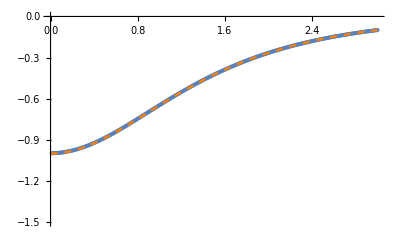

```mathematica
p1=ListPlot[{aVals[[2;;]],intVals}ᵀ,PlotRange->{-1.5,0}];
p2=Plot[-Sech[a],{a,0,3},PlotStyle->{Orange,Dashed}];
Show[{p1,p2}]
```

So we can conclude that the integrand is always positive. The sign is therefore determined only by the coefficient g_s, which implies that the inner shock is always unstable.

### Smooth stability transformation groups

#### Original coordinates

```mathematica
eqOg=u0[r]D[u1[t,r], {t,2}]+2 u0[r]D[(u0[r]D[u1[t,r], t]), r]+u0[r]D[(u0[r]D[((u0[r]-1/u0[r])u1[t,r]), r]), r]//
Collect[#,{D[u1[t,r], {t,2}],D[u1[t,r], {r,2}],D[u1[t,r], t,r],D[u1[t,r], t],D[u1[t,r], r],u1[t,r]},Expand]&
```

u1[t,r] (-u0'[r]^2/u0[r]+u0[r] u0'[r]^2+u0''[r]+u0[r]^2 u0''[r])+(u0'[r]+3 u0[r]^2 u0'[r]) u1^(0,1)[t,r]+(-u0[r]+u0[r]^3) u1^(0,2)[t,r]+2 u0[r] u0'[r] u1^(1,0)[t,r]+2 u0[r]^2 u1^(1,1)[t,r]+u0[r] u1^(2,0)[t,r]

```mathematica
eqOg/u0[r]-(D[u1[t,r], {t,2}]-D[(D[((1-u0[r]^2)u1[t,r]), r] - 2u0[r]D[u1[t,r], t]+D[(1/2 u0[r]^2-Log[-u0[r]]), r]u1[t,r]), r])//Simplify(*Collect[#,{∂_{t,2} u1[t,r],∂_{r,2} u1[t,r],∂_(t,r) u1[t,r],∂_t u1[t,r],∂_r u1[t,r],u1[t,r]},Expand]&*)
```

0

```mathematica
(D[u1[t,r], {t,2}]-D[(D[((1-u0[r]^2)u1[t,r]), r] - 2u0[r]D[u1[t,r], t]+D[(1/2 u0[r]^2-Log[-u0[r]]), r]u1[t,r]), r])-(
D[u1[t,r], {t,2}]+D[(  2u0[r]D[u1[t,r], t]+u0[t,r]D[((u0[r]+1/u0[r])u1[t,r]), r]), r])//FullSimplify
```

1/u0[r]^3(u1[t,r] (-2 u0[t,r] u0'[r]^2+u0[r]^2 u0''[r]+u0[r]^4 u0''[r]+u0[r]^3 (u0'[r]^2-u0[t,r] u0''[r]-u0'[r] u0^(0,1)[t,r])+u0[r] (u0[t,r] u0''[r]+u0'[r] (-u0'[r]+u0^(0,1)[t,r])))+u0[r] (((u0[r]+3 u0[r]^3+2 u0[t,r]-2 u0[r]^2 u0[t,r]) u0'[r]-u0[r] (1+u0[r]^2) u0^(0,1)[t,r]) u1^(0,1)[t,r]+u0[r] (u0[r] (-1+u0[r]^2)-(1+u0[r]^2) u0[t,r]) u1^(0,2)[t,r]))

#### Defining an energy functional

```mathematica
vecs={D[u[t,r], {t,2}],D[u[t,r], t,r],D[u[t,r], {r,2}],D[u[t,r], t],D[u[t,r], r],u[t,r]};
```

```mathematica
D[u[t,r], {t,2}]/.utt//Collect[#,vecs]&
```

```mathematica
energy=1/2(Subscript[e, 1][r](D[(u[t,r]), t])^2+Subscript[e, 2][r](D[u[t,r], t]+Subscript[e, 3][r]D[u[t,r], r])^2+Subscript[e, 4][r](D[(Subscript[e, 5][r]u[t,r]), r])^2+(Subscript[e, 6][r]u[t,r])^2)//Collect[#,vecs,Simplify]&
```

1/2 u[t,r]^2 (e_6[r]^2+e_4[r] e_5'[r]^2)+u[t,r] e_4[r] e_5[r] e_5'[r] u^(0,1)[t,r]+1/2 (e_2[r] e_3[r]^2+e_4[r] e_5[r]^2) (u^(0,1)[t,r])^2+e_2[r] e_3[r] u^(0,1)[t,r] u^(1,0)[t,r]+1/2 (e_1[r]+e_2[r]) (u^(1,0)[t,r])^2

```mathematica
waveEq=D[u[t,r], {t,2}]->(
Subscript[f, 1,1][r]D[u[t,r], t,r]
+ Subscript[f, 0,2][r]D[u[t,r], {r,2}]
+Subscript[f, 1,0][r]D[u[t,r], t]
+Subscript[f, 0,1][r]D[u[t,r], r]
+Subscript[f, 0,0][r]u[t,r]);
```

```mathematica
(D[energy, t]/.waveEq//MonomialList[#,vecs]&//TableForm)/.{f_[r]->f,f_[t,r]->f}
```

(e_2 e_3+e_1 f_(1,1)+e_2 f_(1,1)) u^(1,0) u^(1,1)
(e_2 e_3^2+e_4 e_5^2+e_2 e_3 f_(1,1)) u^(0,1) u^(1,1)
u e_4 e_5 e_5' u^(1,1)
(e_1 f_(0,2)+e_2 f_(0,2)) u^(0,2) u^(1,0)
e_2 e_3 f_(0,2) u^(0,1) u^(0,2)
(e_1 f_(1,0)+e_2 f_(1,0)) (u^(1,0))^2
(e_1 f_(0,1)+e_2 f_(0,1)+e_2 e_3 f_(1,0)+e_4 e_5 e_5') u^(0,1) u^(1,0)
u (e_6^2+e_1 f_(0,0)+e_2 f_(0,0)+e_4 (e_5')^2) u^(1,0)
e_2 e_3 f_(0,1) (u^(0,1))^2
u e_2 e_3 f_(0,0) u^(0,1)

```mathematica
sols={
Subscript[f, 0,2]->(Subscript[e, 2][#](Subscript[e, 3][#])^2/(Subscript[e, 1][#])&),
Subscript[f, 1,0]->(D[(Subscript[e, 1][#]Subscript[f, 1,1][#]), #]/(2 Subscript[e, 1][#])&),
Subscript[f, 0,1]->(D[(Subscript[e, 2][#](Subscript[e, 3][#])^2), #]/(Subscript[e, 1][#])&),
Subscript[f, 0,0]->((Subscript[e, 3][#]D[(Subscript[e, 2][#]Subscript[e, 3]'[#]), #]-(Subscript[e, 4][#])^2)/(Subscript[e, 1][#])&),
Subscript[g, 0]->(Subscript[e, 2][#]Subscript[e, 3][#]Subscript[e, 3]'[#]&),
Subscript[g, 1]->(Subscript[e, 2][#](Subscript[e, 3][#])^2&),
Subscript[g, 2]->(Subscript[e, 1][#](Subscript[f, 1,1][#])/2&)
};
```

General Inner Product (Not sure how to enforce positive definiteness)

```mathematica
x={D[u[t,r], t],D[u[t,r], r],u[t,r]};
mm={{Subscript[m, 1,1][r],Subscript[m, 1,2][r],Subscript[m, 1,3][r]},
{Subscript[m, 1,2][r],Subscript[m, 2,2][r],Subscript[m, 2,3][r]},
{Subscript[m, 1,3][r],Subscript[m, 2,3][r],Subscript[m, 3,3][r]}};
nn={{Subscript[n, 1,1][r],Subscript[n, 1,2][r],Subscript[n, 1,3][r]},
{Subscript[n, 1,2][r],Subscript[n, 2,2][r],Subscript[n, 2,3][r]},
{Subscript[n, 1,3][r],Subscript[n, 2,3][r],Subscript[n, 3,3][r]}};
```

```mathematica
x.mm.x//MonomialList[#,vecs]&//TableForm
```

m_(1,1)[r] (u^(1,0)[t,r])^2
2 m_(1,2)[r] u^(0,1)[t,r] u^(1,0)[t,r]
2 u[t,r] m_(1,3)[r] u^(1,0)[t,r]
m_(2,2)[r] (u^(0,1)[t,r])^2
2 u[t,r] m_(2,3)[r] u^(0,1)[t,r]
u[t,r]^2 m_(3,3)[r]

```mathematica
clean={f_[r]->f,f_[t,r]->f};
```

```mathematica
(x.nn.x//MonomialList[#,vecs]&//TableForm)/.clean
```

n_(1,1) (u^(1,0))^2
2 n_(1,2) u^(0,1) u^(1,0)
2 u n_(1,3) u^(1,0)
n_(2,2) (u^(0,1))^2
2 u n_(2,3) u^(0,1)
u^2 n_(3,3)

```mathematica
(1/2 D[(x.mm.x), t]/.waveEq//MonomialList[#,vecs]&//TableForm)/.clean
```

(f_(1,1) m_(1,1)+m_(1,2)) u^(1,0) u^(1,1)
(f_(1,1) m_(1,2)+m_(2,2)) u^(0,1) u^(1,1)
u (f_(1,1) m_(1,3)+m_(2,3)) u^(1,1)
f_(0,2) m_(1,1) u^(0,2) u^(1,0)
f_(0,2) m_(1,2) u^(0,1) u^(0,2)
u f_(0,2) m_(1,3) u^(0,2)
(f_(1,0) m_(1,1)+m_(1,3)) (u^(1,0))^2
(f_(0,1) m_(1,1)+f_(1,0) m_(1,2)+m_(2,3)) u^(0,1) u^(1,0)
u (f_(0,0) m_(1,1)+f_(1,0) m_(1,3)+m_(3,3)) u^(1,0)
f_(0,1) m_(1,2) (u^(0,1))^2
u (f_(0,0) m_(1,2)+f_(0,1) m_(1,3)) u^(0,1)
u^2 f_(0,0) m_(1,3)

```mathematica
coeffs=(D[((x.mm.x)/2), t]-D[((x.nn.x)/2), r]/.waveEq//MonomialList[#,vecs]&)/.{Derivative[i_,j_][u][t,r]->1,u[t,r]->1};
```

```mathematica
ms={Subscript[m, 1,1][r],Subscript[m, 1,2][r],Subscript[m, 1,3][r],Subscript[m, 2,2][r],Subscript[m, 2,3][r],Subscript[m, 3,3][r]};
ns={Subscript[n, 1,1][r],Subscript[n, 1,2][r],Subscript[n, 1,3][r],Subscript[n, 2,2][r],Subscript[n, 2,3][r],Subscript[n, 3,3][r]};
```

```mathematica
{A,coeffM}=CoefficientArrays[coeffs,Join[ms,ns,D[ms, r],D[ns, r]]];
```

```mathematica
meqs={
coeffs[[2]]-coeffs[[4]],
D[coeffs[[1]], r]-2 coeffs[[7]],
D[coeffs[[3]], r]-coeffs[[9]],
coeffs[[8]]-coeffs[[3]]-D[coeffs[[4]], r],
2coeffs[[10]]-2coeffs[[6]]-D[coeffs[[5]], r],
2coeffs[[12]]-D[(coeffs[[11]]-D[coeffs[[6]], r]), r]
}//Simplify;
meqs/.f_[r]->f//TableForm
```

-f_(0,2) m_(1,1)+f_(1,1) m_(1,2)+m_(2,2)
-2 f_(1,0) m_(1,1)-2 m_(1,3)+m_(1,1) f_(1,1)'+f_(1,1) m_(1,1)'+m_(1,2)'
-f_(0,0) m_(1,1)-f_(1,0) m_(1,3)-m_(3,3)+m_(1,3) f_(1,1)'+f_(1,1) m_(1,3)'+m_(2,3)'
f_(0,1) m_(1,1)+f_(1,0) m_(1,2)-f_(1,1) m_(1,3)-m_(1,1) f_(0,2)'-f_(0,2) m_(1,1)'
2 f_(0,1) m_(1,2)-m_(1,2) f_(0,2)'-f_(0,2) (2 m_(1,3)+m_(1,2)')
-m_(1,2) f_(0,0)'-m_(1,3) f_(0,1)'+f_(0,0) (2 m_(1,3)-m_(1,2)')-f_(0,1) m_(1,3)'+2 f_(0,2)' m_(1,3)'+m_(1,3) f_(0,2)''+f_(0,2) m_(1,3)''

```mathematica
fsols={
Solve[meqs[[1]]==0,Subscript[f, 1,1][r]][[1]][[1]],
Solve[meqs[[2]]==0,Subscript[f, 1,0][r]][[1]][[1]],
Solve[meqs[[3]]==0,Subscript[f, 0,0][r]][[1]][[1]],
Solve[meqs[[4]]==0,Subscript[f, 0,1][r]][[1]][[1]]};
```

```mathematica
cond1=meqs[[5]]/.fsols[[4]]/.fsols[[3]]/.fsols[[2]]/.fsols[[1]]/.D[(fsols[[1]]), r]//FullSimplify
```

1/(m_(1,1)[r])^2((m_(1,2)[r])^2 (2 m_(1,3)[r]-m_(1,2)'[r])-m_(1,1)[r] m_(2,2)[r] (2 m_(1,3)[r]+m_(1,2)'[r])+m_(1,2)[r] (m_(2,2)[r] m_(1,1)'[r]+m_(1,1)[r] m_(2,2)'[r]))

Wow. This is completely independent of the choices of f! So it must be saying something about the differentiable structure of the inner product

```mathematica
cond2=meqs[[6]]/.fsols[[4]]/.D[fsols[[4]], r]/.fsols[[3]]/.D[fsols[[3]], r]/.fsols[[2]]/.D[fsols[[2]], r]/.fsols[[1]]/.D[fsols[[1]], r]//FullSimplify
```

1/(m_(1,1)[r])^3(2 m_(1,3)[r] m_(1,1)'[r] (m_(2,2)[r] m_(1,1)'[r]+m_(1,2)[r] (2 m_(1,3)[r]-m_(1,2)'[r]))+m_(1,1)[r] (2 (m_(1,3)[r])^3-3 (m_(1,3)[r])^2 m_(1,2)'[r]-2 m_(2,2)[r] m_(1,1)'[r] m_(1,3)'[r]+m_(1,2)[r] (m_(1,2)'[r] m_(1,3)'[r]+m_(1,1)'[r] (-m_(3,3)[r]+m_(2,3)'[r]))+m_(1,3)[r] ((m_(1,2)'[r])^2-m_(1,1)'[r] m_(2,2)'[r]-m_(2,2)[r] m_(1,1)''[r]+m_(1,2)[r] (-4 m_(1,3)'[r]+m_(1,2)''[r])))+(m_(1,1)[r])^2 (m_(1,3)'[r] m_(2,2)'[r]-(2 m_(1,3)[r]-m_(1,2)'[r]) (m_(3,3)[r]-m_(2,3)'[r])+m_(2,2)[r] m_(1,3)''[r]+m_(1,2)[r] (m_(3,3)'[r]-m_(2,3)''[r])))

```mathematica
(Subscript[m, 1,1][r])^2 cond1/.Subscript[m, 1,3][r]->0/.Subscript[m, 1,2]->(0&)//Expand
```

0

```mathematica
(Subscript[m, 1,1][r])^2 cond2/.Subscript[m, 1,3]->(0&)/.Subscript[m, 1,2]->(0&)//Simplify
```

0

If I set m_(1,2) and m_(1,3) (the ∂_t u ∂_r u and ∂_t u u terms) to zero, then the consistency conditions are automatically satisfied.

```mathematica
fsimple={
Subscript[f, 0,2][r]->(Subscript[m, 2,2][r])/(Subscript[m, 1,1][r]),
(*Subscript[f, 1,1]->((Subscript[f, 1,1][#])/(Subscript[m, 1,1][#])&),*)
Subscript[f, 1,0][r]->D[(Subscript[m, 1,1][r]Subscript[f, 1,1][r]), r]/(2 Subscript[m, 1,1][r]),
Subscript[f, 0,1][r]->(Subscript[m, 2,2]'[r])/(Subscript[m, 1,1][r]),
Subscript[f, 0,0][r]->(Subscript[m, 2,3]'[r]-Subscript[m, 3,3][r])/(Subscript[m, 1,1][r])};
```

```mathematica
nsols={Solve[coeffs[[1]]==0,Subscript[n, 1,1][r]][[1]][[1]],
Solve[coeffs[[2]]==0,Subscript[n, 1,2][r]][[1]][[1]],
Solve[coeffs[[3]]==0,Subscript[n, 1,3][r]][[1]][[1]],
Solve[coeffs[[5]]==0,Subscript[n, 2,2][r]][[1]][[1]],
Solve[coeffs[[6]]==0,Subscript[n, 2,3][r]][[1]][[1]],
Subscript[n, 3,3][r]->0};
```

```mathematica
esimple={Subscript[m, 1,2]->(0&),Subscript[m, 1,3]->(0&),Subscript[m, 2,3]->(0&),Subscript[m, 3,3]->(0&)};
```

```mathematica
(x.nn.x)/2/.nsols/.esimple//Expand
```

m_(2,2)[r] u^(0,1)[t,r] u^(1,0)[t,r]+1/2 f_(1,1)[r] m_(1,1)[r] (u^(1,0)[t,r])^2

```mathematica
D[((x.mm.x)/2), t]-D[((x.nn.x)/2), r]/.waveEq/.nsols/.D[nsols, r]/.fsimple/.D[fsimple, r]/.esimple//FullSimplify
```

0

```mathematica
fsimple/.{Subscript[m, 2,3]->(0&),Subscript[m, 3,3]->(0&)}
```

{f_(0,2)[r]→(m_(2,2)[r])/(m_(1,1)[r]),f_(1,0)[r]→(m_(1,1)[r] f_(1,1)'[r]+f_(1,1)[r] m_(1,1)'[r])/(2 m_(1,1)[r]),f_(0,1)[r]→(m_(2,2)'[r])/(m_(1,1)[r]),f_(0,0)[r]→0}

```mathematica
nsols/.{Subscript[m, 1,2]->(0&),Subscript[m, 1,3]->(0&)}//TableForm
```

n_(1,1)[r]→f_(1,1)[r] m_(1,1)[r]
n_(1,2)[r]→m_(2,2)[r]
n_(1,3)[r]→m_(2,3)[r]
n_(2,2)[r]→0
n_(2,3)[r]→0
n_(3,3)[r]→0

We have:

```mathematica
wave=D[v[t,r], {t,2}]->1/(Subscript[m, 1,1][r])(D[(Subscript[m, 2,2][r]D[v[t,r], r]+Subscript[f, 1,1][r]D[v[t,r], t]), r]);
```

```mathematica
energy=1/2(Subscript[m, 1,1][r](D[v[t,r], t])^2+Subscript[m, 2,2][r](D[v[t,r], r])^2);
```

```mathematica
nsols/.esimple//TableForm
```

n_(1,1)[r]→f_(1,1)[r] m_(1,1)[r]
n_(1,2)[r]→m_(2,2)[r]
n_(1,3)[r]→0
n_(2,2)[r]→0
n_(2,3)[r]→0
n_(3,3)[r]→0

```mathematica
wave
```

v^(2,0)[t,r]→1/(m_(1,1)[r])(m_(2,2)'[r] v^(0,1)[t,r]+m_(2,2)[r] v^(0,2)[t,r]+f_(1,1)'[r] v^(1,0)[t,r]+f_(1,1)[r] v^(1,1)[t,r])

```mathematica
(D[energy, t]-D[(Subscript[m, 2,2][r]Derivative[0,1][v][t,r] Derivative[1,0][v][t,r]+1/2 Subscript[f, 1,1][r]  (Derivative[1,0][v][t,r])^2), r])/.wave//Expand
```

1/2 f_(1,1)'[r] (v^(1,0)[t,r])^2

Let’s just write the solution

```mathematica
realWave=D[u[t,r], {t,2}]->D[(-Subscript[u, 0][r](2 D[u[t,r], t]+D[((Subscript[u, 0][r]-1/(Subscript[u, 0][r]))u[t,r]), r])), r];
```

```mathematica
realEnergy=1/2((Subscript[u, 0][r]-1/(Subscript[u, 0][r]))(D[u[t,r], t])^2-Subscript[u, 0][r](D[((Subscript[u, 0][r]-1/(Subscript[u, 0][r]))u[t,r]), r])^2);
```

```mathematica
realDiff=-Subscript[u, 0][r](Subscript[u, 0][r]-1/(Subscript[u, 0][r]))D[u[t,r], t](D[((Subscript[u, 0][r]-1/(Subscript[u, 0][r]))u[t,r]), r]+D[u[t,r], t]);
```

```mathematica
D[(realEnergy), t]-D[(realDiff), r]/.realWave//Simplify
```

(2 u_0'[r] (u^(1,0)[t,r])^2)/u_0[r]

### Smooth stability modes

```mathematica
vars={u,δ,ℓ};
smoothlinearisedEqs=eqsUnsteady/.ur->u/.OverTilde[f_]->(ε f̃[#1,#2]&)//SeriesCoefficient[#,{ε,0,1}]&//Map[(Collect[#,ϵ]&),#]&;
expandSteady=(OverBar[f_]/;MemberQ[vars,f])->(Sum[ϵ^i Subscript[f̄, i][#1],{i,0,1}]&);
expandUnsteady=(OverTilde[f_]/;MemberQ[vars,f])->(Sum[ϵ^i Subscript[f̃, i][#1,#2],{i,0,1}]&);
steadyOuterSol={
Subscript[δ̄, 0]->(-Log[- # Subscript[ū, 0][#]]&),Subscript[q̄, 0]->(1/# D[# Subscript[ū, 0][#],#]&),
Subscript[ℓ̄, 0]->(ℓ&)};
```

```mathematica
smoothAsymptoticEqs=smoothlinearisedEqs/.expandSteady/.expandUnsteady;
smoothAsymptoticEqs=Table[Map[SeriesCoefficient[#,{ϵ,0,i}]&,smoothAsymptoticEqs],{i,0,1}]/.steadyOuterSol//Simplify;
```

#### Deriving the wave equation

```mathematica
x=.
```

```mathematica
ClearAll[v]
```

```mathematica
lfreeeq=smoothAsymptoticEqs[[1]]/.Subscript[ℓ̃, 0]->(0&);
```

```mathematica
linearpert=(D[lfreeeq[[1]], r] - (D[lfreeeq[[2]], t]+Subscript[ū, 0]'[r]lfreeeq[[2]]+Subscript[ū, 0][r]D[lfreeeq[[2]], r])//Simplify//Expand)/.{Subscript[ũ, 0]->Subscript[u, 1],Subscript[ū, 0]->Subscript[u, 0]};
```

```mathematica
linearpert+(D[Subscript[u, 1][t,r], {t,2}]+D[(Subscript[u, 0][r](2 D[Subscript[u, 1][t,r], t]+D[((Subscript[u, 0][r]-1/(Subscript[u, 0][r]))Subscript[u, 1][t,r]), r])), r])//Expand
```

0

```mathematica
linearEq=D[Subscript[u, 1][t,r], {t,2}]+D[(Subscript[u, 0][r](2 D[Subscript[u, 1][t,r], t]+D[((Subscript[u, 0][r]-1/(Subscript[u, 0][r]))Subscript[u, 1][t,r]), r])), r];
```

```mathematica
linearEq
```

u_0'[r] (u_1[t,r] (u_0'[r]+u_0'[r]/u_0[r]^2)+(-1/u_0[r]+u_0[r]) u_1^(0,1)[t,r]+2 u_1^(1,0)[t,r])+u_0[r] (u_1[t,r] (-(2 u_0'[r]^2)/u_0[r]^3+u_0''[r]+u_0''[r]/u_0[r]^2)+2 (u_0'[r]+u_0'[r]/u_0[r]^2) u_1^(0,1)[t,r]+(-1/u_0[r]+u_0[r]) u_1^(0,2)[t,r]+2 u_1^(1,1)[t,r])+u_1^(2,0)[t,r]

```mathematica
linearEq//Collect[#,{Subscript[u, 1][t,r],D[Subscript[u, 1][t,r], t],D[Subscript[u, 1][t,r], r],D[Subscript[u, 1][t,r], {t,2}],D[Subscript[u, 1][t,r], {r,2}],D[Subscript[u, 1][t,r], t,r]},Simplify]&
```

(u_1[t,r] ((-1+u_0[r]^2) u_0'[r]^2+u_0[r] (1+u_0[r]^2) u_0''[r]))/u_0[r]^2+((1+3 u_0[r]^2) u_0'[r] u_1^(0,1)[t,r])/u_0[r]+(-1+u_0[r]^2) u_1^(0,2)[t,r]+2 u_0'[r] u_1^(1,0)[t,r]+2 u_0[r] u_1^(1,1)[t,r]+u_1^(2,0)[t,r]

```mathematica
inner=a[r]D[(b[r]Subscript[u, 1][t,r]), t]+c[r]D[(b[r]Subscript[u, 1][t,r]), r];
outer=d[r]D[inner, t]+e[r]D[inner, r]//Collect[#,{Subscript[u, 1][t,r],D[Subscript[u, 1][t,r], t],D[Subscript[u, 1][t,r], r],D[Subscript[u, 1][t,r], {t,2}],D[Subscript[u, 1][t,r], {r,2}],D[Subscript[u, 1][t,r], t,r]},Simplify]&
```

e[r] u_1[t,r] (b'[r] c'[r]+c[r] b''[r])+e[r] (2 c[r] b'[r]+b[r] c'[r]) u_1^(0,1)[t,r]+b[r] c[r] e[r] u_1^(0,2)[t,r]+(b[r] e[r] a'[r]+(c[r] d[r]+a[r] e[r]) b'[r]) u_1^(1,0)[t,r]+b[r] (c[r] d[r]+a[r] e[r]) u_1^(1,1)[t,r]+a[r] b[r] d[r] u_1^(2,0)[t,r]

```mathematica
spectrumEq=linearEq/.Derivative[i_,j_][f_]->(λ^i Derivative[j][f][#2]&)/.f_[t,r]->f[r]//Collect[#,{Subscript[u, 1][r],Subscript[u, 1]'[r],Subscript[u, 1]''[r]},Expand]&
```

(2 λ u_0[r]+u_0'[r]/u_0[r]+3 u_0[r] u_0'[r]) u_1'[r]+u_1[r] (λ^2+2 λ u_0'[r]+u_0'[r]^2-u_0'[r]^2/u_0[r]^2+u_0''[r]/u_0[r]+u_0[r] u_0''[r])+(-1+u_0[r]^2) u_1''[r]

```mathematica
spectrumCoordTransform=spectrumEq/.Subscript[u, 1]->(Subscript[v, 1][x[#]]&)/.r->r[x]/.x[r[x]]->x;
```

```mathematica
spectrumCoordTransform
```

x'[r[x]] (2 λ u_0[r[x]]+u_0'[r[x]]/u_0[r[x]]+3 u_0[r[x]] u_0'[r[x]]) v_1'[x]+v_1[x] (λ^2+2 λ u_0'[r[x]]+u_0'[r[x]]^2-u_0'[r[x]]^2/u_0[r[x]]^2+u_0''[r[x]]/u_0[r[x]]+u_0[r[x]] u_0''[r[x]])+(-1+u_0[r[x]]^2) (v_1'[x] x''[r[x]]+x'[r[x]]^2 v_1''[x])

```mathematica
transEq=spectrumCoordTransform/.f_[r[x]]->f/.Derivative[i_][Subscript[v, j_]][x]->Derivative[i][Subscript[v, j]]/.Subscript[v, j_][x]->Subscript[v, j]//Simplify//Collect[#,{Subscript[v, 1],Subscript[v, 1]',Subscript[v, 1]''},Expand]&
```

v_1' (2 λ u_0 x'+(x' u_0')/u_0+3 u_0 x' u_0'-x''+u_0^2 x'')+v_1 (λ^2+2 λ u_0'+(u_0')^2-(u_0')^2/u_0^2+u_0''/u_0+u_0 u_0'')+(-(x')^2+u_0^2 (x')^2) v_1''

#### Integral of velocity

Rewrite equation as integral

```mathematica
linearEq-D[(D[ψ[t,r], {t,2}]+Subscript[u, 0][r]D[(2 D[ψ[t,r], t]+((Subscript[u, 0][r]-1/(Subscript[u, 0][r]))D[ψ[t,r], r])), r]), r]/.Subscript[u, 1]->(D[ψ[#1,#2], #2]&)//Simplify
```

0

Normal modes

```mathematica
spectrumEqR=D[ψ[t,r], {t,2}]+Subscript[u, 0][r](2 D[ψ[t,r], t,r]+D[((Subscript[u, 0][r]-1/(Subscript[u, 0][r]))D[ψ[t,r], r]), r])/.Derivative[i_,j_][f_]->(λ^i Derivative[j][f][#2]&)/.f_[t,r]->f[r]
```

λ^2 ψ[r]+u_0[r] (2 λ ψ'[r]+ψ'[r] (u_0'[r]+u_0'[r]/u_0[r]^2)+(-1/u_0[r]+u_0[r]) ψ''[r])

Coordinate transform

```mathematica
spectrumEqX=spectrumEqR/.ψ->(v[x[#]]&)/.r->r[x]/.x[r[x]]->x//Collect[#,{v[x],v'[x],v''[x]}]&
```

λ^2 v[x]+u_0[r[x]] (-1/u_0[r[x]]+u_0[r[x]]) x'[r[x]]^2 v''[x]+v'[x] (2 λ u_0[r[x]] x'[r[x]]+u_0[r[x]] x'[r[x]] (u_0'[r[x]]+u_0'[r[x]]/u_0[r[x]]^2)+u_0[r[x]] (-1/u_0[r[x]]+u_0[r[x]]) x''[r[x]])

```mathematica
spectrumEqXF=spectrumEqX/f[λ,x]/.v->(f[λ,#]w[#]&)//Collect[#,{w[x],w'[x],w''[x]},Simplify]&
```

(-1+u_0[r[x]]^2) x'[r[x]]^2 w''[x]+w'[x] ((x'[r[x]] u_0'[r[x]])/u_0[r[x]]+u_0[r[x]] x'[r[x]] (2 λ+u_0'[r[x]])-x''[r[x]]+u_0[r[x]]^2 x''[r[x]]+(2 (-1+u_0[r[x]]^2) x'[r[x]]^2 f^(0,1)[λ,x])/f[λ,x])+1/f[λ,x]w[x] (λ^2 f[λ,x]+1/u_0[r[x]](2 λ u_0[r[x]]^2 x'[r[x]]+(1+u_0[r[x]]^2) x'[r[x]] u_0'[r[x]]+u_0[r[x]] (-1+u_0[r[x]]^2) x''[r[x]]) f^(0,1)[λ,x]+(-1+u_0[r[x]]^2) x'[r[x]]^2 f^(0,2)[λ,x])

```mathematica
cleanupToX={r[x]->r,Derivative[i_][x][r]->Derivative[i][x],
f_[r]->f};
```

```mathematica
spectrumEqXF/.cleanupToX
```

(-1+u_0[r]^2) x'[r]^2 w''[x]+w'[x] ((x'[r] u_0'[r])/u_0[r]+u_0[r] x'[r] (2 λ+u_0'[r])-x''[r]+u_0[r]^2 x''[r]+(2 (-1+u_0[r]^2) x'[r]^2 f^(0,1)[λ,x])/f[λ,x])+1/f[λ,x]w[x] (λ^2 f[λ,x]+1/u_0[r](2 λ u_0[r]^2 x'[r]+(1+u_0[r]^2) x'[r] u_0'[r]+u_0[r] (-1+u_0[r]^2) x''[r]) f^(0,1)[λ,x]+(-1+u_0[r]^2) x'[r]^2 f^(0,2)[λ,x])

```mathematica
coordsX={x'[r]->(-Subscript[u, 0][r])/((Subscript[u, 0][r])^2-1),f[λ,x]->E^(λ x)};
```

```mathematica
((Subscript[u, 0][r])^2-1)spectrumEqXF/.r[x]->r/.coordsX/.D[coordsX[[1]], r]/.D[coordsX[[2]], x]/.D[coordsX[[2]], {x,2}]//Collect[#,{w[x],w'[x],w''[x]},Simplify]&
```

-λ^2 w[x]+u_0[r]^2 w''[x]